```mathematica
ResourceFunction["MaTeXInstall"][]
```

Paclet[MaTeX,1.7.8,<>]

```mathematica
ImageSize
```

## Q 1 profiles

```mathematica
(*<<MaTeX`*)
Needs["MaTeX`"]
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/N1000/Q1_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
```

```mathematica
radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
```

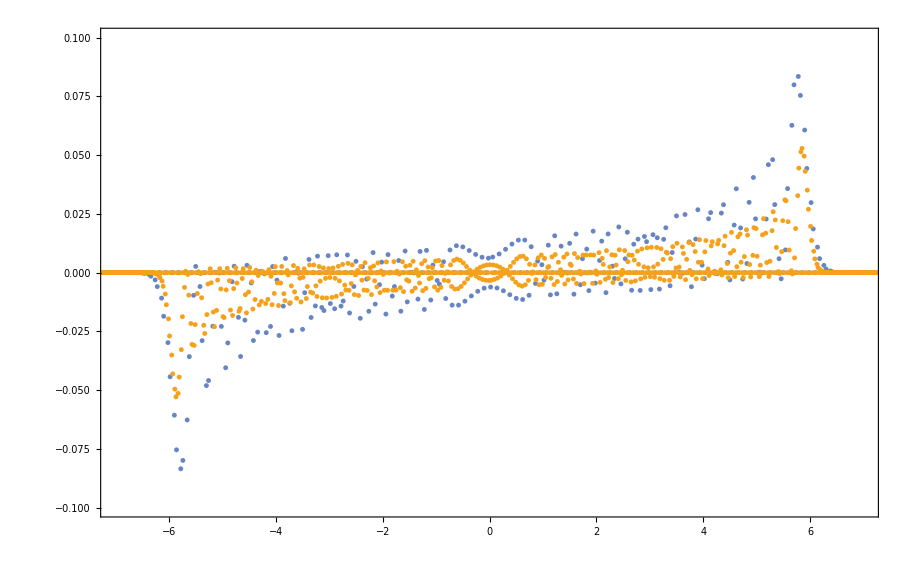

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=50/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=time^0Qexpectation[n,3,time];



FIG=ListPlot[{
(*
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
*)
Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Obs[n,TimeSlice2]},{n,xmin,xmax}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin,xmax}]
},
Joined->{False,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\zeta=\\ell/t","\\mathcal{Q^-}_1(\\ell/t)"},FontSize->35]
,LabelStyle->Directive[FontSize->20]
,LABELS={
(*
"0mod3; t="<>ToString[TimeSlice3*timestep]
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
*)
"t="<>ToString[TimeSlice2*timestep]
,"t="<>ToString[TimeSlice3*timestep]

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 25],{0.8,0.2}]
,PlotRange->{{-7,7},{-0.1,0.1}}
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow, radius}
(*{GREEN0, radius}*)
}
 ]
```

```mathematica
1.5*1.5
```

2.25

## Q1 for a single site

```mathematica
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
(*Data=Import["Data/Sav/DownUpUp/Correlation3.dat"];*)

site=0;
column =3;

Data=Import["UUD/N1000/Q1_profile.dat"];
Data=Drop[Data,1];
Data=DeleteCases[Data,_?(Length[#]<4&)];
Data=Cases[Data,_?(#[[1]]==0+site&)];
Data=Data[[;;,{4,column}]];
```

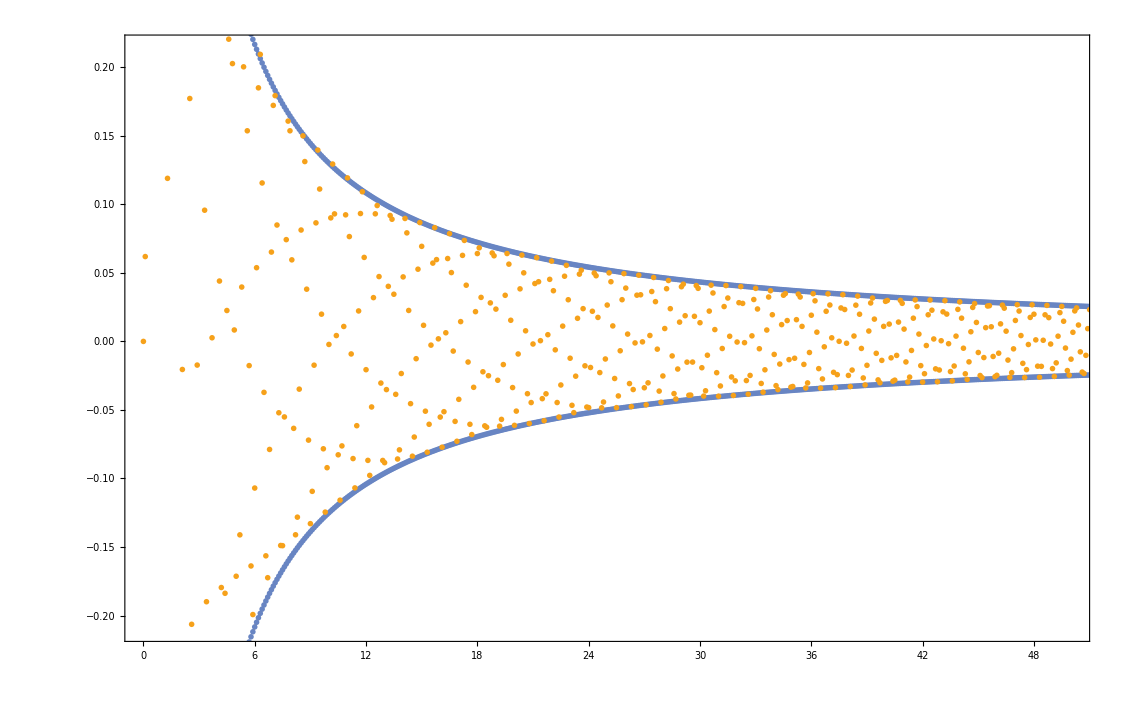

```mathematica
Needs["MaTeX`"]
<<MaTeX`

radius=0.015;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
SciPostBlack = Graphics[{RGBColor[0/255,0/255,0/255],Disk[]}];
SciPostRed = Graphics[{RGBColor[1,0.11,0.14],Disk[]}];

ListPlot[{
Table[{Data[[k,1]],1.3/Data[[k,1]]},{k,2,Length[Data]}],
Table[{Data[[k,1]],-1.25/Data[[k,1]]},{k,2,Length[Data]}],
Table[{Data[[k,1]],4Data[[k,2]]},{k,1,Length[Data]}]
}
,PlotRange->{{0,50},{Automatic,Automatic}}
,PlotStyle->PointSize[Medium]
,Joined->{True,True,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{False,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","\\langle {\\mathcal{Q}}_{\\ell} \\rangle"},FontSize->35]
,LabelStyle->Directive[FontSize->25]
,PlotLegends->{Placed[MaTeX[{
"1/t",
"\\ell = 0"


},FontSize->20],{0.8,0.15}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{

{SciPostBlue,radius},
{SciPostBlue,radius},
{SciPostYellow,radius}


}

]
```

## Q 2 profiles

```mathematica
(*<<MaTeX`*)
Needs["MaTeX`"];
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/N1000/Q2_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
```

```mathematica
radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
```

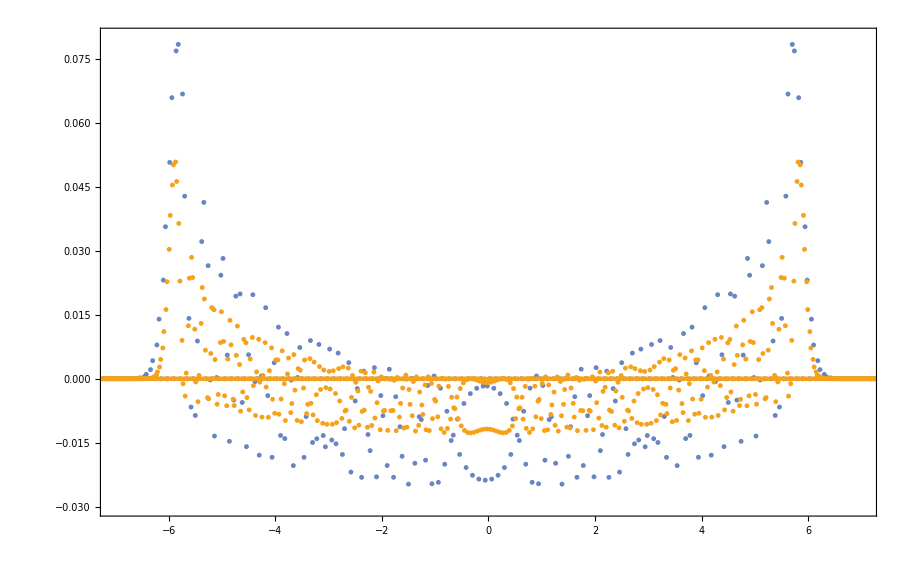

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=50/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=time^0Qexpectation[n,2,time];



FIG=ListPlot[{
(*
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
*)

Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Obs[n,TimeSlice2]},{n,xmin,xmax}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin,xmax}]
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->False
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","\\mathcal{Q^+}_2(\\ell/t)"},FontSize->35]
,LabelStyle->Directive[FontSize->25]
,LABELS={
(*
"0mod3; t="<>ToString[TimeSlice3*timestep]
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
*)
"t="<>ToString[TimeSlice2*timestep]
,"t="<>ToString[TimeSlice3*timestep]
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 20],{0.5,0.8}]
,PlotRange->{{-7,7},{-0.03,0.08}}
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow, radius}
}
 ]
```

## Q 1 Q2 integrated profiles vs t

```mathematica
(*<<MaTeX`*)
Needs["MaTeX`"]
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Q2_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/Q2_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

```mathematica
(*RUN this part also*)
Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=Qexpectation[n,2,time];
FIG=ListPlot[{
Table[ {TimeSlice, Sum[Obs[n,TimeSlice/timestep],{n,xmin,xmax}]
} ,{TimeSlice,0,timestep TimeSlice3,timestep}]
(*,Avalanche*)
(*,Table[
{TimeSlice, Sum[Obs2[n,TimeSlice],{n,xmin,xmax}]} ,{TimeSlice,0, TimeSlice3,1}]*)
},
Joined->False
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","\\sum_x \\mathcal{Q}^{\\pm}_{x}(t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"t="<>ToString[TimeSlice3*timestep]
,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{0,TimeSlice3 timestep},{Automatic,Automatic}}
,PlotMarkers->{
{BLUE0,radius},
{RED0, radius}
}
 ]
```

-Graphics-

## Q 1 Q2 averaged profiles

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/Q1_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/Q1_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=60/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=time^1Qexpectation[n,3,time];

AvrgData={};
AverWindow =3;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
(*If[Abs[obs]>10^-6,*)
average +=obs;
counter++;
;

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}]

FIG=ListPlot[{
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+0,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,3}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+2,xmax,3}]
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","t\\mathcal{Q^-}_1(\\ell/t)"},FontSize->16]
,LabelStyle->Directive[FontSize->12]
,LABELS={
"0mod3; t="<>ToString[TimeSlice3*timestep]
(*,"Avrg Over "<>ToString[AverWindow]<>"Sites"*)
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"1mod3; t="<>ToString[TimeSlice3*timestep]
,"2mod3; t="<>ToString[TimeSlice3*timestep]
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{1.0,0.6}]
,PlotRange->{{-7,7},{-12,12}}
,PlotMarkers->{
{BLUE0,radius},
{RED0, radius},
{GREEN0, radius}
}
 ]
```

-Graphics-

```mathematica
Averaging[window_,{
AvrgData={};
AverWindow =window;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
If[Abs[obs]>10^-6,
{average +=obs;
counter++;
}];

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}];
Return AvrgData;
}]
```

Averaging[window_,{Null}]

## {(S^z)_(3l+a)(t)} UUD profile

```mathematica
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/SxSySz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[σ^x, l], (σ^y)_(l,)Subscript[σ^z, l]*)
(*A=Cases[A,_?(Mod[#[[1]],2]==0&)];*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize;
timestep=0.1;
<<MaTeX`;
TimeSlice1 = 10/timestep;
TimeSlice2 = 60/timestep;
SHIFT=1;
(*technical part:  point types etc *)
radius=10;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];


RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];

everypoint=3;

P[l_,time_,col_]:=A[[l+SystemSize*Floor[time],col]];
Obs[l_,time_]:=  P[l,time,2];
FIG=ListPlot[{
  (*  Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin,xmax,everypoint}]*)
Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin,xmax,everypoint}]

(* ,Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin+1,xmax,everypoint}]*),Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin+1,xmax,everypoint}]

(*,Table[{(P[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), 2P[l,TimeSlice1,4]},{l,xmin+2,xmax,everypoint}]*),Table[{(P[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), 2P[l,TimeSlice2,4]},{l,xmin+2,xmax,everypoint}]

},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->False,
Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\sigma^z_{\\ell}"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
(*"\\sigma^z_{3\\ell}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell}(t="<>ToString[TimeSlice2*timestep]<>")",

(*"\\sigma^z_{3\\ell+1}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell+1}(t="<>ToString[TimeSlice2*timestep]<>")",

(*"\\sigma^z_{3\\ell+2}(t="<>ToString[TimeSlice1*timestep]<>")",*)
"\\sigma^z_{3\\ell+2}(t="<>ToString[TimeSlice2*timestep]<>")"


},FontSize->12],{1.,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{GREEN0,radius}
,{BLUE0,radius}
,{RED0, radius}
(*,{BLUE,radius}*)

(*,{BLUE0,radius}*)
(*,{RED1,radius}*)

(*,{BLACK,0.008},{BLACK,0.008}*)
}

 ]
```

Import::nffil: File ~/Programs/Folded_XXZ_GS/Data/UUD/SxSySz_profile.dat not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,1].

Drop::argm: Drop called with 0 arguments; 1 or more arguments are expected.

-Graphics-

## S^vN profiles

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/N1000/Entropy_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=10;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
```

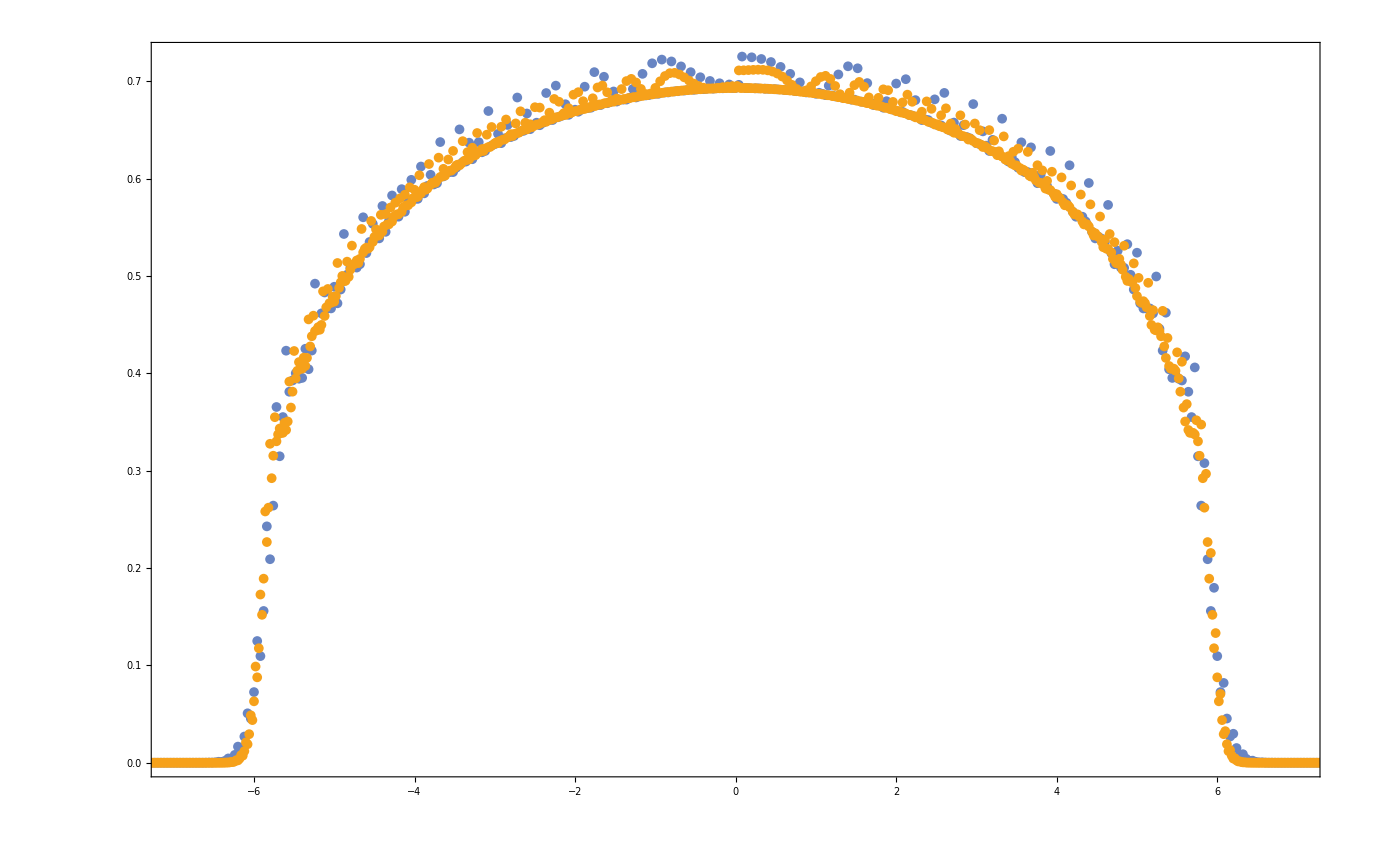

```mathematica
(*RUN this part also*)
timestep=0.1;
TimeSlice0=10;
TimeSlice1=25/timestep;
TimeSlice3=50/timestep;


Qexpectation[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
(*To change Subscript[Q, 1]^- -> Subscript[Q, 1]^+ one should change 3->2 below*)
Obs[n_,time_]:=Qexpectation[n,2,time];

AvrgData={};
AverWindow =1;
TimeSlice=TimeSlice3;
(*For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
(*If[Abs[obs]>10^-6,*)
average +=obs;
counter++;
;

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}]*)

FIG=ListPlot[{
Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax,1}],
Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin,xmax,1}]
(*Table[{n,√(1/2)+1.2(1+-1/(√(1-(n/6)^2)))},{n,-5.9,5.9,0.01}]*)
(*,Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin,xmax}]*)
(*,AvrgData*)
(*,{0} *)(*This is technical thing to match plot frame boxes with other plots
I add it to use legenda sigma^x ...
*)
},
Joined->{False,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\ell/t","\\mathcal{S}_{vN}(\\ell/t)"},FontSize->30]
,LabelStyle->Directive[FontSize->20]
,LABELS={
"t="<>ToString[TimeSlice1*timestep]
(*,"Avrg Over "<>ToString[AverWindow]<>"Sites"*)
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"t="<>ToString[TimeSlice3*timestep]
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 20],{0.5,0.4}]
,PlotRange->{{-7,7},{Automatic,Automatic}}
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow, radius}
}
 ]
```

```mathematica
Averaging[window_,{
AvrgData={};
AverWindow =window;
TimeSlice=TimeSlice3;
For[l=xmin, l<xmax, l+=AverWindow,{
average = 0;
counter=0;
For[l0=0,l0<AverWindow,l0++,{
If[l0+l>xmax, {Break[]}];
obs=Obs[l+l0,TimeSlice];
If[Abs[obs]>10^-6,
{average +=obs;
counter++;
}];

}];
If[counter==0,counter++];
average /=counter;
AppendTo[AvrgData,{(l+Floor[AverWindow/2]-Floor[(xmax-xmin)/2]-2)/(TimeSlice*timestep),average}];
}];
Return AvrgData;
}]
```

Averaging[window_,{Null}]

## S^vN Center

```mathematica
<<MaTeX`
A=Import["~/Programs/Folded_XXZ_GS/Data/UUD/N1000/Entropy_center.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)

radius=5;
widht=Thickness[0.2];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
```

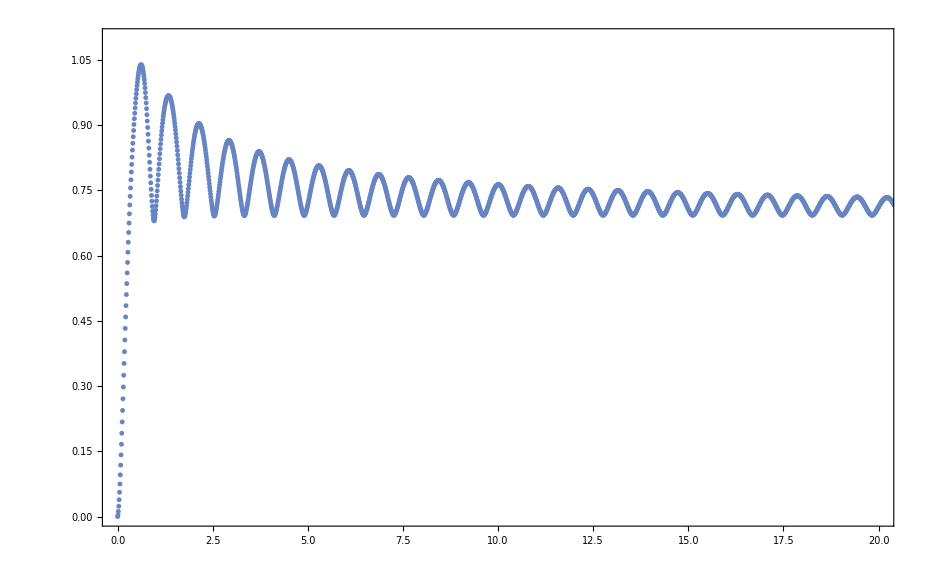

```mathematica
FIG=ListPlot[{
Table[{A[[n,1]],A[[n,2]]},{n,1,Length[A]}]
},
Joined->{False,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","\\mathcal{S}_{vN}(t)"},FontSize->30]
,LabelStyle->Directive[FontSize->20]
,LABELS={
"\ell=0"
(*,"\\sigma^x(t="<>ToString[TimeSlice1]<>")"*)

};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 20],{0.5,0.4}]
,PlotRange->{{0,20},{0,1.1}}
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow, radius}
}
 ]
```

## ED

```mathematica
L=9;
SX=SparseArray[{Band[{2,1}]->0},{2,2}];
SY=SparseArray[{Band[{1,2}]->0},{2,2}];
SZ=SparseArray[{Band[{1,1}]->0},{2,2}];
un=SparseArray[{Band[{1,1}]->1},{2,2}];
SX[[1,2]]=1.;SX[[2,1]]=1;
SY[[1,2]]=-ⅈ;SY[[2,1]]=ⅈ;
SZ[[1,1]]=1;SZ[[2,2]]=-1;

Table[sz[j]=KroneckerProduct@@Join[Table[un,j-1],{SZ},Table[un,L-j]],{j,L}];
Table[sx[j]=KroneckerProduct@@Join[Table[un,j-1],{SX},Table[un,L-j]],{j,L}];
Table[sy[j]=KroneckerProduct@@Join[Table[un,j-1],{SY},Table[un,L-j]],{j,L}];
b[j_]:= 1/2(sx[j].sy[j+1].sz[j+2]-sy[j].sx[j+1] .sz[j+2]
-(sz[j-1].sx[j].sy[j+1]- sz[j-1].sy[j].sx[j+1])
);
A[j_]:= sx[j].sy[j+1]-sy[j].sx[j+1] ;
B=Sum[b[j],{j,2,L-2}];


up = {1.,0};
down = {0,1.};
left = {1./(√2),-1/(√2)};
right= {1./(√2),1./(√2)};
JIS = KroneckerProduct[up,up,up,down,down,up,down,down,down]//Flatten;
(*
JIS = KroneckerProduct[up,down]//Flatten;
JIS.A[1].JIS
*)
JIS.MatrixExp[B].JIS
```

SetDelayed::write: Tag Drop in Drop[][j_] is Protected.

6.3843+0. ⅈ

```mathematica
A[1].JIS//MatrixForm//Chop
```

Drop[][1].{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1.,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
JIS
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

## XXZ large and diff Delta

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

XXZ5=Import["XXZ/Delta5_N300_2/Sz_profile.dat"];
XXZ5=Drop[XXZ5,1];
XXZ5=DeleteCases[XXZ5,_?(Length[#]<4&)];
XXZ5=Chop[XXZ5[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

XXZ10=Import["XXZ/Delta10_N263/Sz_profile.dat"];
XXZ10=Drop[XXZ10,1];
XXZ10=DeleteCases[XXZ10,_?(Length[#]<4&)];
XXZ10=Chop[XXZ10[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

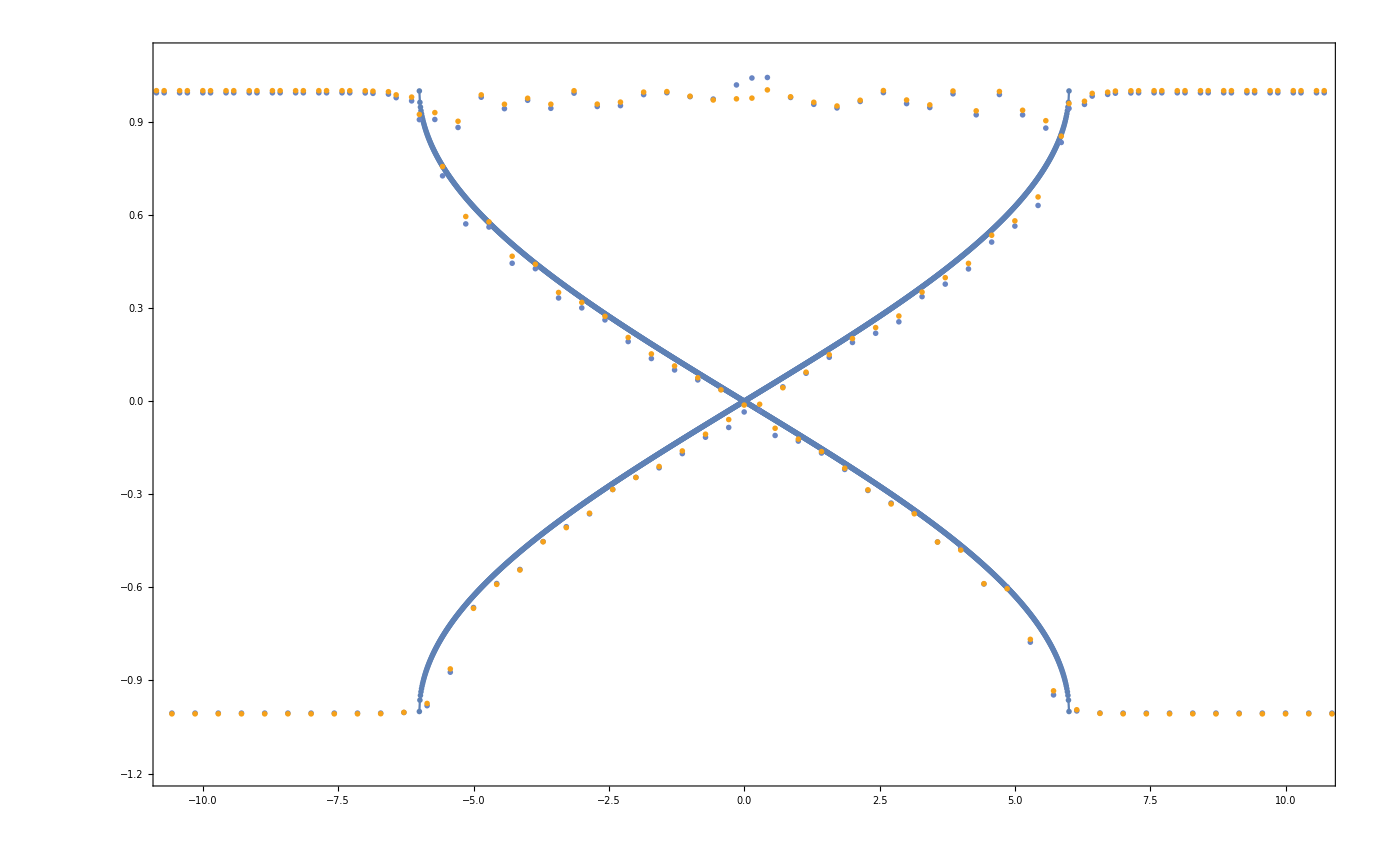

```mathematica
Needs["MaTeX`"]

Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

Sites=XXZ5[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ5 =Length[Sites]; 
xminXXZ5=1;
xmaxXXZ5=SystemSizeXXZ5;


Sites=XXZ10[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ10 =Length[Sites]; 
xminXXZ10=1;
xmaxXXZ10=SystemSizeXXZ10;


timestep=0.1;

Time = 7.;

TimeSlice1 = Time/timestep;
TimeSliceXXZ5 =Time/timestep;
TimeSliceXXZ10 = Time/(timestep (*π/(4 *10.)*));
SHIFT=1;(*technical part:  point types etc *)

radius=0.01;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],widht}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];



everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

DataXXZ5[l_,time_,col_]:=XXZ5[[l+SystemSizeXXZ5*Floor[time],col]];
ObsXXZ5[l_,time_]:= 4DataXXZ5[l,time,3];

DataXXZ10[l_,time_,col_]:=XXZ10[[l+SystemSizeXXZ10*Floor[time],col]];
ObsXXZ10[l_,time_]:= 4DataXXZ10[l,time,3];


FIG=ListPlot[{
Join[Table[{ζ,2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}],Table[{ζ,-2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}]]

(*,Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]
*)
,Table[{(DataXXZ5[l,TimeSliceXXZ5,1]+SHIFT)/(TimeSliceXXZ5*timestep),1.27( (ObsXXZ5[l,TimeSliceXXZ5])-0.05)},{l,xminXXZ5,xmaxXXZ5,everypoint}]
,Table[{(DataXXZ10[l,TimeSliceXXZ10,1]+SHIFT)/(TimeSliceXXZ10*timestep), 1.045((ObsXXZ10[l,TimeSliceXXZ10])-0.01)},{l,xminXXZ10,xmaxXXZ10,everypoint}]
},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{True,False,False}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\zeta=\\ell/t","\\langle \\sigma^z_{\\ell}\\sigma^z_{\\ell+1} \\rangle"},FontSize->35],
LabelStyle->Directive[FontSize->25],
PlotLegends->{Placed[MaTeX[{
"{\\rm folded}\\quad \\sigma^z_{\\ell}(t \\to \\infty)"
(*,"Folded (numerics)\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSlice1*timestep]<>")"*)
,"\\Delta=5\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ5*timestep]<>")"
,"\\Delta=10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ10*timestep]<>")"
},FontSize->20],{0.5,0.15}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{BLACK,radius}
,{SciPostBlue,radius}
,{SciPostYellow,radius}
(*,{RED0, radius}*)
}

 ]
```

## XXZ large Delta collapse

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

(*XXZ=Import["XXZ/Delta5_N363/Sz_profile.dat"];*)
XXZ=Import["XXZ/Delta10_N263/Sz_profile.dat"];
XXZ=Drop[XXZ,1];
XXZ=DeleteCases[XXZ,_?(Length[#]<4&)];
XXZ=Chop[XXZ[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

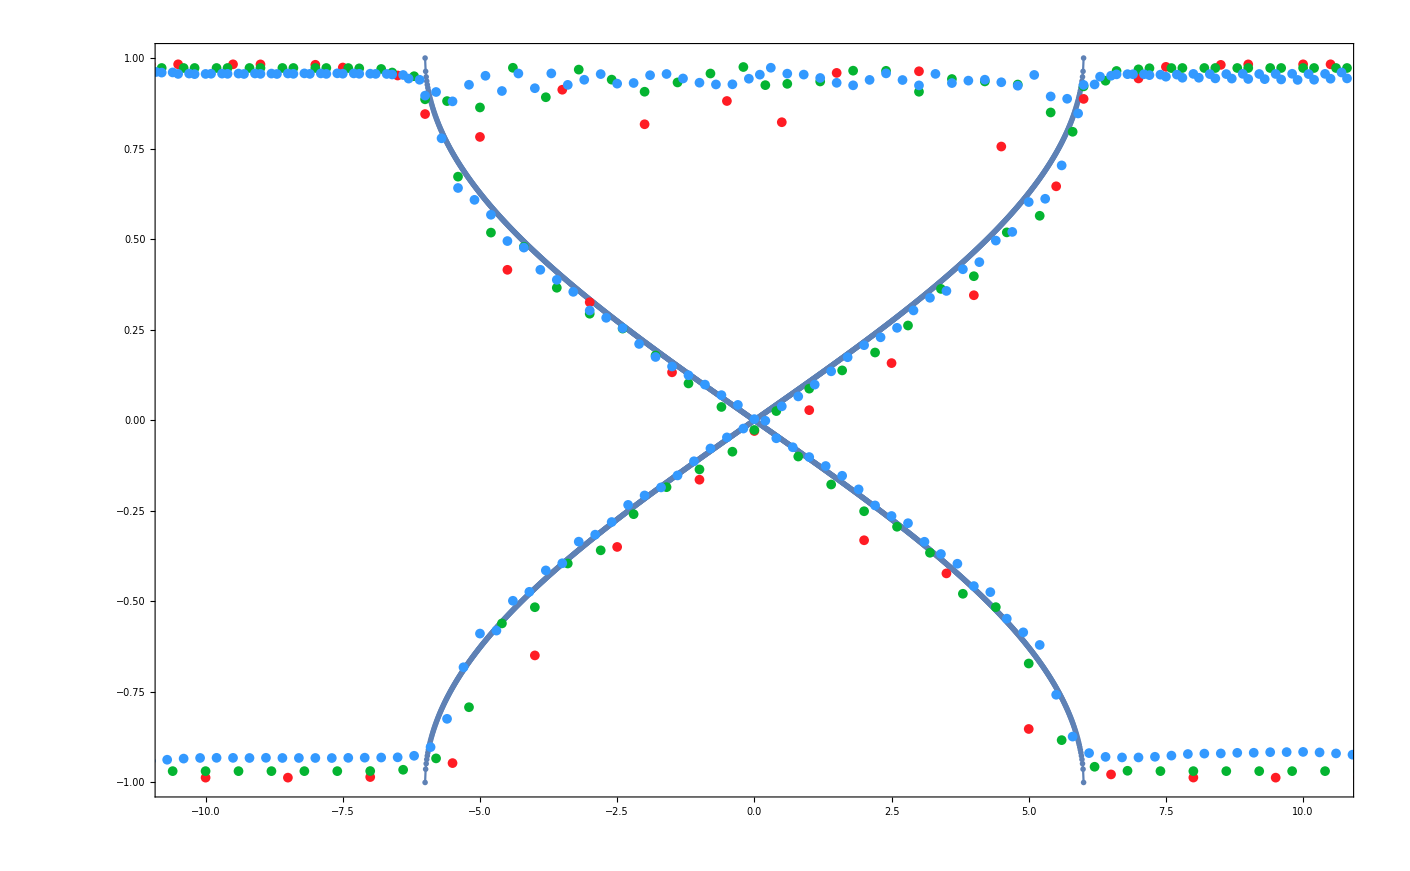

```mathematica
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

Sites=XXZ[[;;,1]];
Sites=Union[Sites];
SystemSizeXXZ =Length[Sites]; 
xminXXZ=1;
xmaxXXZ=SystemSizeXXZ;

timestep=0.1;
Time = 10.;

TimeSlice1 = Time/timestep;
TimeSliceXXZ2 =2.0/timestep;
TimeSliceXXZ3 =5.0/timestep;
TimeSliceXXZ4 =Time/timestep;
SHIFT=1;(*technical part:  point types etc *)

radius=10.;
width=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],width,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],width,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],width,Disk[]}];
BLACK0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],width,Disk[]}];



everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

DataXXZ[l_,time_,col_]:=XXZ[[l+SystemSizeXXZ*Floor[time],col]];
ObsXXZ[l_,time_]:= 4DataXXZ[l,time,3];


FIG=ListPlot[{
Join[Table[{ζ,2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}],Table[{ζ,-2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}]]
(*,Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]*)
,Table[{(DataXXZ[l,TimeSliceXXZ2,1]+SHIFT)/(TimeSliceXXZ2*timestep), (ObsXXZ[l,TimeSliceXXZ2])},{l,xminXXZ,xmaxXXZ,everypoint}]
,Table[{(DataXXZ[l,TimeSliceXXZ3,1]+SHIFT)/(TimeSliceXXZ3*timestep), (ObsXXZ[l,TimeSliceXXZ3])},{l,xminXXZ,xmaxXXZ,everypoint}]
,Table[{(DataXXZ[l,TimeSliceXXZ4,1]+SHIFT)/(TimeSliceXXZ4*timestep), (ObsXXZ[l,TimeSliceXXZ4])},{l,xminXXZ,xmaxXXZ,everypoint}]
},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{True,False,False,False}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\langle \\sigma^z_{\\ell}\\sigma^z_{\\ell+1} \\rangle"},FontSize->16],
LabelStyle->Directive[FontSize->12],
PlotLegends->{Placed[MaTeX[{
"Folded (analyt)\\quad \\sigma^z_{\\ell}(t \\to \\infty)"
(*,"Folded (numerics)\\quad \\sigma^z_{\\ell}(t="<>ToString[TimeSlice1*timestep]<>")"*)
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ2*timestep]<>")"
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ3*timestep]<>")"
,"XXZ-10\\quad \\sigma^z_{\\ell}\\sigma^z_{\\ell+1}(t="<>ToString[TimeSliceXXZ4*timestep]<>")"
},FontSize->20],{0.85,0.5}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{BLACK,radius}
(*,{BLACK0,radius}*)
,{RED0,radius}
,{GREEN0,radius}
,{BLUE0, radius}
}

 ]
```

```mathematica
Export["../Pictures/Simply_Jammed/XXZ10.pdf",Out[300]];
```

```mathematica
0.01 π/(4.*16)16
```

0.00785398

## Folded magnetization collapse with a scaling curve

```mathematica
Needs["MaTeX`"];
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

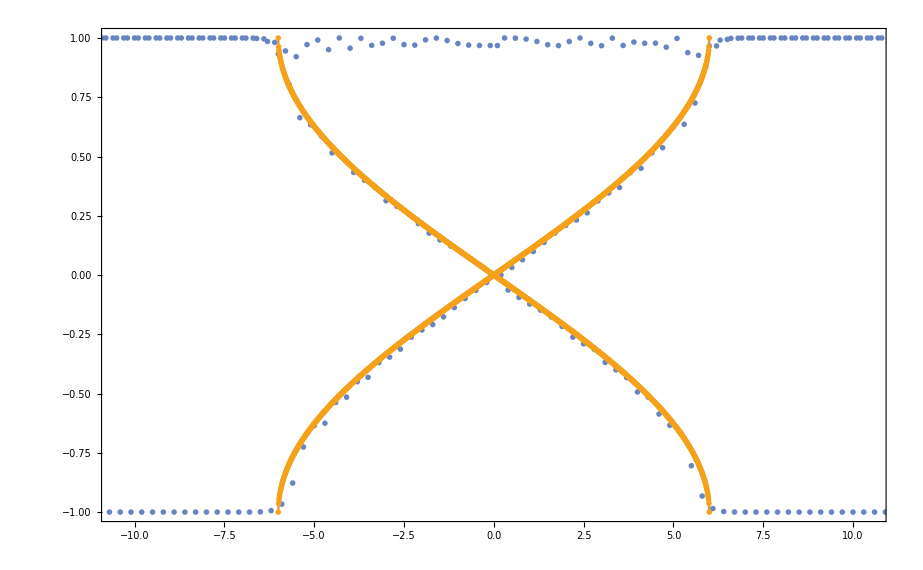

```mathematica
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

timestep=0.1;
Time = 10;

TimeSlice1 = Time/timestep;
SHIFT=1;(*technical part:  point types etc *)


<<MaTeX`
radius = 0.015;
width = 0.01;
RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],width,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],width,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],width,Disk[]}];
BLACK0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],width,Disk[]}];

SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];


everypoint=1;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= 2 DataFolded[l,time,2];

FIG=ListPlot[{

Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep), (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]
,Join[Table[{ζ,2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}],Table[{ζ,-2/π ArcSin[ζ/6]},{ζ,-10,10,0.01}]]
},
PlotRange->{{-10.5,10.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{False,True}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\zeta=\\ell/t","\\langle \\sigma^z_{\\ell} \\rangle"},FontSize->35],
LabelStyle->Directive[FontSize->25],
PlotLegends->{Placed[MaTeX[{
"{\\rm Numerics}\\quad \\sigma^z_{\\ell}(t="<>ToString[TimeSlice1*timestep]<>")"
,"{\\rm Analytics}\\quad \\sigma^z_{\\ell}(t \\to \\infty)"

},FontSize->20],{0.5,0.15}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{SciPostBlue,radius}
,{SciPostYellow,radius}

(*,{GREEN0,radius}
,{BLUE0, radius}
*)}

 ]
```

```mathematica
Export["../Pictures/Simply_Jammed/XXZ10.pdf",Out[300]];
```

```mathematica
0.01 π/(4.*16)16
```

0.00785398

## Jamming criterium ⟨(1-(σ^z)_l)/2(1-(σ^z)_(l+1))/2⟩≡[⟨(σ^z)_l(σ^z)_(l+1)⟩ – ⟨(σ^z)_l⟩-⟨(σ^z)_(l+1)⟩ ++1 ]/4 Profile

```mathematica
Needs["MaTeX`"];
<<MaTeX`
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
```

```mathematica
LenData={{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,1.6943*10^-10},{67,1.6943*10^-10},{68,9.21368*10^-10},{69,4.75264*10^-9},{70,4.75264*10^-9},{71,2.32061*10^-8},{72,1.07016*10^-7},{73,1.07016*10^-7},{74,4.64923*10^-7},{75,1.8975*10^-6},{76,1.8975*10^-6},{77,7.25235*10^-6},{78,0.0000258648},{79,0.0000258648},{80,0.0000857196},{81,0.000262724},{82,0.000262724},{83,0.000740452},{84,0.00190584},{85,0.00190584},{86,0.0044421},{87,0.00927507},{88,0.00927507},{89,0.0171036},{90,0.0273089},{91,0.0273089},{92,0.0366587},{93,0.0394137},{94,0.0394137},{95,0.0309105},{96,0.0139089},{97,0.0139089},{98,0.000934775},{99,0.00435072},{100,0.00435072},{101,0.0194346},{102,0.0246782},{103,0.0246782},{104,0.0108339},{105,9.29244*10^-7},{106,9.29244*10^-7},{107,0.0111268},{108,0.0215248},{109,0.0215248},{110,0.0085709},{111,0.000694868},{112,0.000694868},{113,0.0157577},{114,0.0154443},{115,0.0154443},{116,0.000302302},{117,0.0110564},{118,0.0110564},{119,0.0163313},{120,0.000512765},{121,0.000512765},{122,0.0112958},{123,0.0139944},{124,0.0139944},{125,0.0000328163},{126,0.0150997},{127,0.0150997},{128,0.0074705},{129,0.00389106},{130,0.00389106},{131,0.0161234},{132,0.000190673},{133,0.000190673},{134,0.0142524},{135,0.00540227},{136,0.00540227},{137,0.00744913},{138,0.0116691},{139,0.0116691},{140,0.00235226},{141,0.0150243},{142,0.0150243},{143,0.000318863},{144,0.0159125},{145,0.0159125},{146,1.13417*10^-6},{147,0.0158857},{148,0.0158857},{149,0.0000542711},{150,0.0158857},{151,1.13417*10^-6},{152,1.13417*10^-6},{153,0.0159125},{154,0.000318863},{155,0.000318863},{156,0.0150243},{157,0.00235226},{158,0.00235226},{159,0.0116691},{160,0.00744913},{161,0.00744913},{162,0.00540227},{163,0.0142524},{164,0.0142524},{165,0.000190673},{166,0.0161234},{167,0.0161234},{168,0.00389106},{169,0.0074705},{170,0.0074705},{171,0.0150997},{172,0.0000328163},{173,0.0000328163},{174,0.0139944},{175,0.0112958},{176,0.0112958},{177,0.000512765},{178,0.0163313},{179,0.0163313},{180,0.0110564},{181,0.000302302},{182,0.000302302},{183,0.0154443},{184,0.0157577},{185,0.0157577},{186,0.000694868},{187,0.0085709},{188,0.0085709},{189,0.0215248},{190,0.0111268},{191,0.0111268},{192,9.29244*10^-7},{193,0.0108339},{194,0.0108339},{195,0.0246782},{196,0.0194346},{197,0.0194346},{198,0.00435072},{199,0.000934775},{200,0.000934775},{201,0.0139089},{202,0.0309105},{203,0.0309105},{204,0.0394137},{205,0.0366587},{206,0.0366587},{207,0.0273089},{208,0.0171036},{209,0.0171036},{210,0.00927507},{211,0.0044421},{212,0.0044421},{213,0.00190584},{214,0.000740452},{215,0.000740452},{216,0.000262724},{217,0.0000857196},{218,0.0000857196},{219,0.0000258648},{220,7.25235*10^-6},{221,7.25235*10^-6},{222,1.8975*10^-6},{223,4.64923*10^-7},{224,4.64923*10^-7},{225,1.07016*10^-7},{226,2.32061*10^-8},{227,2.32061*10^-8},{228,4.75264*10^-9},{229,9.21368*10^-10},{230,9.21368*10^-10},{231,1.6943*10^-10},{232,0},{233,0},{234,0},{235,0},{236,0},{237,0},{238,0},{239,0},{240,0},{241,0},{242,0},{243,0},{244,0},{245,0},{246,0},{247,0},{248,0},{249,0},{250,0},{251,0},{252,0},{253,0},{254,0},{255,0},{256,0},{257,0},{258,0},{259,0},{260,0},{261,0},{262,0},{263,0},{264,0},{265,0},{266,0},{267,0},{268,0},{269,0},{270,0},{271,0},{272,0},{273,0},{274,0},{275,0},{276,0},{277,0},{278,0},{279,0},{280,0},{281,0},{282,0},{283,0},{284,0},{285,0},{286,0},{287,0},{288,0},{289,0},{290,0},{291,0},{292,0},{293,0},{294,0},{295,0},{296,0},{297,0},{298,0},{299,0}};
```

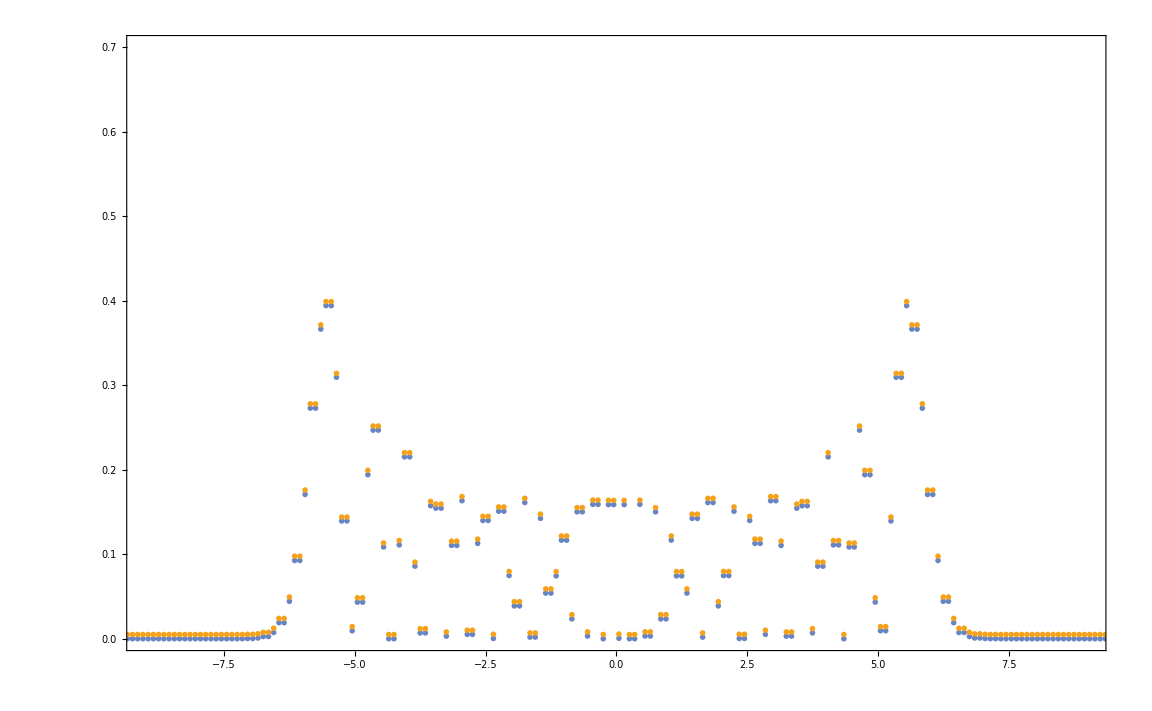

```mathematica
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1(*0.011193*);
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=25/timestep;
TimeSlice3=50/timestep;

radius=0.01;
widht=Thickness[0.002];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];


SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];


Sigma[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
Obs[n_,time_]:=(timestep time)^(1.0)( 4Sigma[n,3,time]  -2(Sigma[n+1,2,time] +Sigma[n,2,time])  + 1)/4;
FIG=ListPlot[{

(*Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Obs[n,TimeSlice2]},{n,xmin+1,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin+1,xmax,1}]

,Table[{n,0.16/(√(1-(n/6)^2))},{n,-5.9,5.9,0.1}]
(*,Table[{n,0.32/(√(12/π Sin[π (n+6)/12]))},{n,-15.9,15.9,0.01}]*)
*)
Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep),Obs[n,TimeSlice1]},{n,xmin+1,xmax,1}]
,Table[{(LenData[[n,1]]-Length[LenData]/2+1)/10,10 LenData[[n,2]]+0.005},{n,1,Length[LenData]}]

},
Joined->{False,False,True}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\zeta=\\ell/t","t\\mathcal{P}_{\\downarrow \\downarrow}(\\ell/t)"},FontSize->35]

(*\\langle \\frac{1-\\sigma^z_{\\ell}}{2}\\frac{1-\\sigma^z_{\\ell+1}}{2} \\rangle*)
,LabelStyle->Directive[FontSize->25]
,LABELS={
(*"t="<>ToString[TimeSlice2*timestep]
,"t="<>ToString[TimeSlice3*timestep]
,"a/\\sqrt{1-(\\zeta/v_{\\pm}) ^2}"
*)
"DMRG \\ t="<>ToString[TimeSlice1*timestep]
,"Lenart \\ t="<>ToString[TimeSlice1*timestep]


};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 30],{0.5,0.8}]
,PlotRange->{{-9,9},{Automatic,0.7(*0.025*)}}
(*,FrameTicks->{
{{0,{0.02,""},{0.04,""},{0.06,""},{0.08,""}
,0.1,{0.12,""},{0.14,""},{0.16,""},{0.18,""}
,0.2,{0.22,""},{0.24,""},{0.26,""},{0.28,""}
,0.3},None},
{(*{-6,-4,-2,0,2,4,6}*)Automatic,None}}*)
(*PlotStyle->{RGBColor[1,0.11,0.14],RGBColor[4/255,180/255,49/255],RGBColor[51/255,153/255,1]},*)
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow, radius},
{RED0,0.01}
}

 ]
```

Power::infy: Infinite expression 1/0. encountered.

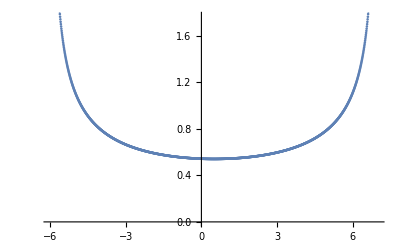

```mathematica
ListPlot[Table[{n,1.1/(√((12+1)/π Sin[π (n+6)/(12+1)]))},{n,-15.9,15.9,0.01}]]
```

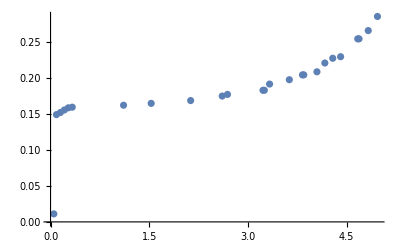

```mathematica
tmpMaxValue=0;
Experim={};
For[n=Floor[(xmax-xmin)/2]+3,n≤ xmax-250, ++n,{
If[Obs[n,TimeSlice3]≥tmpMaxValue ,{
tmpMaxValue=Obs[n,TimeSlice3];
AppendTo[Experim,
 {(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]}]
}];

}]
Experim//ListPlot
```

{k→0.153472}

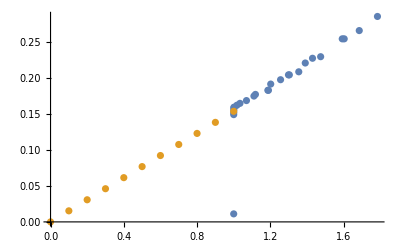

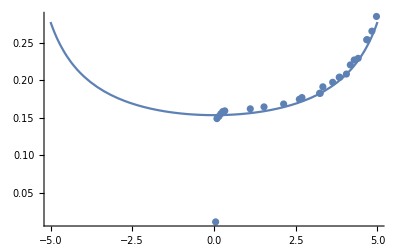

```mathematica
tmpMaxValue=0;
Experim={};
For[n=Floor[(xmax-xmin)/2]+3,n≤ xmax-250, ++n,{
If[Obs[n,TimeSlice3]≥tmpMaxValue ,{
tmpMaxValue=Obs[n,TimeSlice3];
AppendTo[Experim,
 {(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]}]
}];

}]
Experim2=Table[
{
(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]
},{n,Floor[(xmax-xmin)/2]+3,xmax-100}];
ExperimGamma = Table[{1/√(1-(1/6 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Floor[1*Length[Experim]]}];
FIT =FindFit[ExperimGamma,k x,{k},x]

ListPlot[{ExperimGamma,Table[{l,(k/.FIT)l},{l,0,1,0.1}]
}]
Show[
Plot[(k/.FIT)/√(1-(1/6 x)^2) ,{x,-5,5},PlotRange->All]
,ListPlot[Experim]
]
```

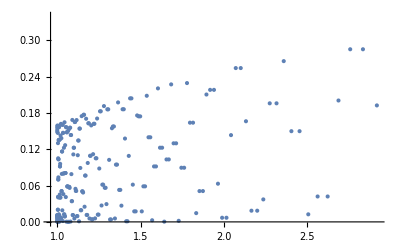

```mathematica
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Length[Experim]}];
ListPlot[ExperimGamma]
```

```mathematica
Table[{n,1.0/(√(1-(n/6)^2))},{n,-6,6,0.1}]
```

Power::infy: Infinite expression 1/0. encountered.

{{-6.,ComplexInfinity},{-5.9,5.50019},{-5.8,3.90567},{-5.7,3.20256},{-5.6,2.78543},{-5.5,2.50217},{-5.4,2.29416},{-5.3,2.13335},{-5.2,2.00446},{-5.1,1.89832},{-5.,1.80907},{-4.9,1.73277},{-4.8,1.66667},{-4.7,1.60875},{-4.6,1.55752},{-4.5,1.51186},{-4.4,1.47087},{-4.3,1.43386},{-4.2,1.40028},{-4.1,1.36966},{-4.,1.34164},{-3.9,1.3159},{-3.8,1.29219},{-3.7,1.27029},{-3.6,1.25},{-3.5,1.23117},{-3.4,1.21367},{-3.3,1.19737},{-3.2,1.18217},{-3.1,1.16797},{-3.,1.1547},{-2.9,1.14229},{-2.8,1.13067},{-2.7,1.11979},{-2.6,1.10959},{-2.5,1.10004},{-2.4,1.09109},{-2.3,1.08271},{-2.2,1.07486},{-2.1,1.06752},{-2.,1.06066},{-1.9,1.05426},{-1.8,1.04828},{-1.7,1.04273},{-1.6,1.03757},{-1.5,1.0328},{-1.4,1.02839},{-1.3,1.02433},{-1.2,1.02062},{-1.1,1.01724},{-1.,1.01419},{-0.9,1.01144},{-0.8,1.00901},{-0.7,1.00688},{-0.6,1.00504},{-0.5,1.00349},{-0.4,1.00223},{-0.3,1.00125},{-0.2,1.00056},{-0.1,1.00014},{0.,1.},{0.1,1.00014},{0.2,1.00056},{0.3,1.00125},{0.4,1.00223},{0.5,1.00349},{0.6,1.00504},{0.7,1.00688},{0.8,1.00901},{0.9,1.01144},{1.,1.01419},{1.1,1.01724},{1.2,1.02062},{1.3,1.02433},{1.4,1.02839},{1.5,1.0328},{1.6,1.03757},{1.7,1.04273},{1.8,1.04828},{1.9,1.05426},{2.,1.06066},{2.1,1.06752},{2.2,1.07486},{2.3,1.08271},{2.4,1.09109},{2.5,1.10004},{2.6,1.10959},{2.7,1.11979},{2.8,1.13067},{2.9,1.14229},{3.,1.1547},{3.1,1.16797},{3.2,1.18217},{3.3,1.19737},{3.4,1.21367},{3.5,1.23117},{3.6,1.25},{3.7,1.27029},{3.8,1.29219},{3.9,1.3159},{4.,1.34164},{4.1,1.36966},{4.2,1.40028},{4.3,1.43386},{4.4,1.47087},{4.5,1.51186},{4.6,1.55752},{4.7,1.60875},{4.8,1.66667},{4.9,1.73277},{5.,1.80907},{5.1,1.89832},{5.2,2.00446},{5.3,2.13335},{5.4,2.29416},{5.5,2.50217},{5.6,2.78543},{5.7,3.20256},{5.8,3.90567},{5.9,5.50019},{6.,ComplexInfinity}}

## Jamming criterium term by term Profile

```mathematica
<<MaTeX`
SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];
(*SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];*)
A=Import["UUD/N1000/Sz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
```

```mathematica
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1(*0.011193*);
TimeSlice0=10;
TimeSlice2=50/timestep;

radius=0.01;
widht=Thickness[0.002];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];

Sigma[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
Obs[n_,time_]:=(timestep time)^(0.0)(4Sigma[n,3,time]  -2(Sigma[n+1,2,time] +Sigma[n,2,time])  + 1)/4;
FIG=ListPlot[{

Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Sigma[n,2,TimeSlice2]},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Sigma[n+1,2,TimeSlice2]},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),(Sigma[n,2,TimeSlice2]+Sigma[n+1,2,TimeSlice2])},{n,xmin,xmax,1}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep),Obs[n,TimeSlice2]},{n,xmin,xmax,1}]

},
Joined->False
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\xi=\\ell/t","\\sigma^z(t)"},FontSize->16]

(*\\langle \\frac{1-\\sigma^z_{\\ell}}{2}\\frac{1-\\sigma^z_{\\ell+1}}{2} \\rangle*)
,LabelStyle->Directive[FontSize->12]
,LABELS={
"\\sigma^z_{\\ell},t="<>ToString[TimeSlice2*timestep]
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"\\sigma^z_{\\ell+1}, t="<>ToString[TimeSlice2*timestep]

,"\\sigma^z_{\\ell}+\\sigma^z_{\\ell+1}, t="<>ToString[TimeSlice2*timestep]
,"\\sigma^z_{\\ell}*\\sigma^z_{\\ell+1}, t="<>ToString[TimeSlice2*timestep]
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 20],{1.,0.5}]
,PlotRange->{{-9,9},{Automatic,Automatic}}
(*,FrameTicks->{
{{0,{0.02,""},{0.04,""},{0.06,""},{0.08,""}
,0.1,{0.12,""},{0.14,""},{0.16,""},{0.18,""}
,0.2,{0.22,""},{0.24,""},{0.26,""},{0.28,""}
,0.3},None},
{(*{-6,-4,-2,0,2,4,6}*)Automatic,None}}*)
(*PlotStyle->{RGBColor[1,0.11,0.14],RGBColor[4/255,180/255,49/255],RGBColor[51/255,153/255,1]},*)
(*,PlotMarkers->{
(*{BLACK,0.25radius},*)
{BLUE0,radius},
(*{GREEN0,radius},*)
{RED0, radius}
}*)

 ]
```

-Graphics-

{k→0.0606857}

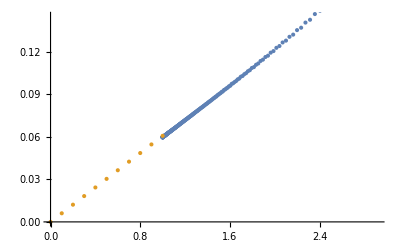

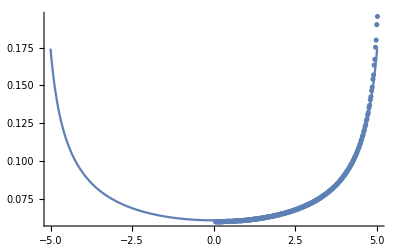

```mathematica
Experim=Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,Floor[(xmax-xmin)/2]+3,xmax-100}];
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Floor[1*Length[Experim]]}];
FIT =FindFit[ExperimGamma,k x,{k},x]

ListPlot[{ExperimGamma,Table[{l,(k/.FIT)l},{l,0,1,0.1}]
}]
Show[
Plot[(k/.FIT)/√(1-(3/16 x)^2) ,{x,-5,5},PlotRange->All]
,ListPlot[Experim]
]
```

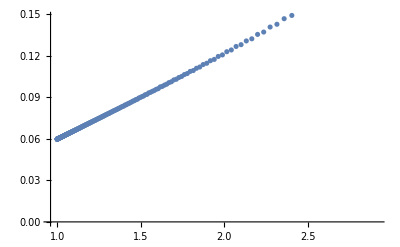

```mathematica
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Length[Experim]}];
ListPlot[ExperimGamma]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Pictures/For_paper/Mathematica.pdf",FIG];
```

## Jamming criterium ⟨(1-(σ^z)_l)/2(1-(σ^z)_(l+1))/2⟩ vs Analytics

```mathematica
<<MaTeX`
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["UUD/N500/Sz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
```

```mathematica
LenData={{1,9.43871*10^-11},{2,9.4387*10^-11},{3,3.44096*10^-10},{4,1.27692*10^-9},{5,1.27692*10^-9},{6,4.63887*10^-9},{7,1.63152*10^-8},{8,5.53439*10^-8},{9,1.80722*10^-7},{10,5.67217*10^-7},{11,1.70852*10^-6},{12,1.70852*10^-6},{13,4.93073*10^-6},{14,4.93073*10^-6},{15,0.0000136093},{16,0.0000136093},{17,0.0000358522},{18,0.0000899423},{19,0.000214317},{20,0.000483618},{21,0.00102989},{22,0.00102989},{23,0.00206132},{24,0.00206132},{25,0.00385849},{26,0.00671376},{27,0.00671376},{28,0.0107759},{29,0.0107759},{30,0.0157945},{31,0.0157945},{32,0.0208523},{33,0.0208523},{34,0.0243081},{35,0.0243081},{36,0.0242501},{37,0.0242501},{38,0.0195905},{39,0.0113874},{40,0.00330057},{41,3.47575*10^-6},{42,0.00369741},{43,0.00369741},{44,0.0112502},{45,0.0155777},{46,0.0119316},{47,0.00370675},{48,0.0000525995},{49,0.00530709},{50,0.00530709},{51,0.0123495},{52,0.0123495},{53,0.0110157},{54,0.0110157},{55,0.00293511},{56,0.00293511},{57,0.000440233},{58,0.000440233},{59,0.00742592},{60,0.0117243},{61,0.00540779},{62,2.72027*10^-6},{63,0.00575898},{64,0.0109399},{65,0.00461429},{66,0.00461429},{67,0.00016616},{68,0.00722639},{69,0.00952973},{70,0.00155692},{71,0.00155692},{72,0.00233271},{73,0.00233271},{74,0.0097265},{75,0.0097265},{76,0.00490692},{77,0.000266176},{78,0.000266176},{79,0.0078875},{80,0.0078875},{81,0.00698865},{82,0.00698865},{83,9.89962*10^-6},{84,0.00643457},{85,0.00763403},{86,0.00763403},{87,0.0000872632},{88,0.0000872632},{89,0.00608891},{90,0.00608891},{91,0.00729694},{92,9.73181*10^-6},{93,9.73181*10^-6},{94,0.00681228},{95,0.00599114},{96,0.000219318},{97,0.00809828},{98,0.00809828},{99,0.00353225},{100,0.00353225},{101,0.00180151},{102,0.00180151},{103,0.00852428},{104,0.000718295},{105,0.00531387},{106,0.00605726},{107,0.000414615},{108,0.00829261},{109,0.00829261},{110,0.0013361},{111,0.00477925},{112,0.00477925},{113,0.00582226},{114,0.00582226},{115,0.000737941},{116,0.000737941},{117,0.00820209},{118,0.00820209},{119,0.000328248},{120,0.00671736},{121,0.00302494},{122,0.00343218},{123,0.00343218},{124,0.00615179},{125,0.000851022},{126,0.000851022},{127,0.00785769},{128,0.00785769},{129,1.31852*10^-7},{130,1.31852*10^-7},{131,0.00787702},{132,0.000578107},{133,0.00684617},{134,0.00684617},{135,0.00181994},{136,0.00181994},{137,0.00550704},{138,0.00309663},{139,0.00433785},{140,0.00408067},{141,0.00408067},{142,0.0035372},{143,0.00467046},{144,0.00467046},{145,0.00314242},{146,0.00486397},{147,0.00486397},{148,0.00314242},{149,0.00314242},{150,0.00467046},{151,0.00467046},{152,0.0035372},{153,0.0035372},{154,0.00408067},{155,0.00408067},{156,0.00433785},{157,0.00433785},{158,0.00309663},{159,0.00309663},{160,0.00550704},{161,0.00181994},{162,0.00181994},{163,0.00684617},{164,0.00684617},{165,0.000578107},{166,0.000578107},{167,0.00787702},{168,0.00787702},{169,1.31852*10^-7},{170,1.31852*10^-7},{171,0.00785769},{172,0.00785769},{173,0.000851022},{174,0.00615179},{175,0.00343218},{176,0.00302494},{177,0.00302494},{178,0.00671736},{179,0.000328248},{180,0.00820209},{181,0.00820209},{182,0.000737941},{183,0.000737941},{184,0.00582226},{185,0.00477925},{186,0.0013361},{187,0.00829261},{188,0.00829261},{189,0.000414615},{190,0.000414615},{191,0.00605726},{192,0.00531387},{193,0.00531387},{194,0.000718295},{195,0.00852428},{196,0.00852428},{197,0.00180151},{198,0.00353225},{199,0.00353225},{200,0.00809828},{201,0.000219318},{202,0.000219318},{203,0.00599114},{204,0.00599114},{205,0.00681228},{206,0.00681228},{207,9.73181*10^-6},{208,9.73181*10^-6},{209,0.00729694},{210,0.00608891},{211,0.0000872632},{212,0.0000872632},{213,0.00763403},{214,0.00643457},{215,9.89962*10^-6},{216,0.00698865},{217,0.00698865},{218,0.0078875},{219,0.0078875},{220,0.000266176},{221,0.00490692},{222,0.0097265},{223,0.00233271},{224,0.00155692},{225,0.00155692},{226,0.00952973},{227,0.00722639},{228,0.00722639},{229,0.00016616},{230,0.00461429},{231,0.0109399},{232,0.0109399},{233,0.00575898},{234,2.72027*10^-6},{235,0.00540779},{236,0.0117243},{237,0.0117243},{238,0.00742592},{239,0.000440233},{240,0.000440233},{241,0.00293511},{242,0.00293511},{243,0.0110157},{244,0.0110157},{245,0.0123495},{246,0.00530709},{247,0.0000525995},{248,0.00370675},{249,0.0119316},{250,0.0119316},{251,0.0155777},{252,0.0112502},{253,0.0112502},{254,0.00369741},{255,3.47575*10^-6},{256,3.47575*10^-6},{257,0.00330057},{258,0.00330057},{259,0.0113874},{260,0.0195905},{261,0.0195905},{262,0.0242501},{263,0.0242501},{264,0.0243081},{265,0.0243081},{266,0.0208523},{267,0.0208523},{268,0.0157945},{269,0.0107759},{270,0.00671376},{271,0.00385849},{272,0.00385849},{273,0.00206132},{274,0.00102989},{275,0.000483618},{276,0.000214317},{277,0.000214317},{278,0.0000899423},{279,0.0000899423},{280,0.0000358522},{281,0.0000358522},{282,0.0000136093},{283,0.0000136093},{284,4.93073*10^-6},{285,4.93073*10^-6},{286,1.70852*10^-6},{287,5.67217*10^-7},{288,1.80722*10^-7},{289,5.53439*10^-8},{290,5.53439*10^-8},{291,1.63152*10^-8},{292,4.63887*10^-9},{293,1.27692*10^-9},{294,1.27692*10^-9},{295,3.44096*10^-10},{296,3.44096*10^-10},{297,9.43871*10^-11},{298,9.43871*10^-11}};
```

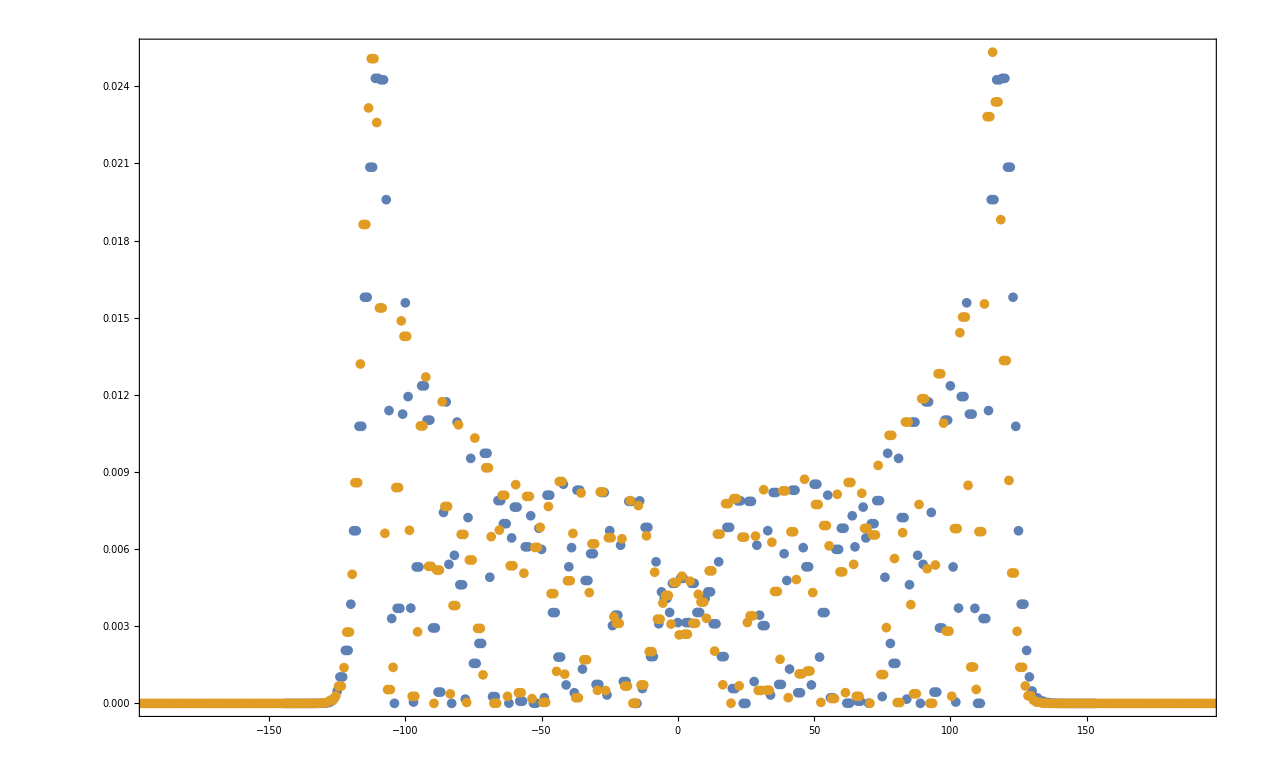

```mathematica
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)


SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1(*0.011193*);
TimeSlice0=10;
TimeSlice1=10/timestep;
TimeSlice2=50/timestep;
TimeSlice3=20./timestep;

radius=0.01;
widht=Thickness[0.002];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];

Sigma[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
Obs[n_,time_]:=(timestep time)^(0.0)( 4Sigma[n,3,time]  -2(Sigma[n+1,2,time] +Sigma[n,2,time])  + 1)/4;
FIG=ListPlot[{
Table[{(LenData[[n,1]]-Length[LenData]/2+4)/1,LenData[[n,2]]},{n,1,Length[LenData]}]
,Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)(TimeSlice3*timestep)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,xmin,xmax,1}]


},
Joined->{False,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\xi=\\ell/t","\\mathcal{P}_{\\downarrow \\downarrow}(\\ell/t)"},FontSize->16]

(*\\langle \\frac{1-\\sigma^z_{\\ell}}{2}\\frac{1-\\sigma^z_{\\ell+1}}{2} \\rangle*)
,LabelStyle->Directive[FontSize->12]
,LABELS={
"Len"
(*,"t="<>ToString[TimeSlice2*timestep]*)
,"DMRG,t="<>ToString[TimeSlice3*timestep]
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 12],{0.95,0.5}]
,PlotRange->{{-190,190},{Automatic,Automatic}}
(*,FrameTicks->{
{{0,{0.02,""},{0.04,""},{0.06,""},{0.08,""}
,0.1,{0.12,""},{0.14,""},{0.16,""},{0.18,""}
,0.2,{0.22,""},{0.24,""},{0.26,""},{0.28,""}
,0.3},None},
{(*{-6,-4,-2,0,2,4,6}*)Automatic,None}}*)
(*PlotStyle->{RGBColor[1,0.11,0.14],RGBColor[4/255,180/255,49/255],RGBColor[51/255,153/255,1]},*)
(*,PlotMarkers->{
(*{BLACK,0.25radius},*)
{BLUE0,radius},
(*{GREEN0,radius},*)
{RED0, radius}
}*)

 ]
```

```mathematica
Experim=Table[{(A[[n+SystemSize*Floor[TimeSlice3],1]]+SHIFT)/(TimeSlice3*timestep),Obs[n,TimeSlice3]},{n,Floor[(xmax-xmin)/2]+3,xmax-100}];
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Floor[1*Length[Experim]]}];
FIT =FindFit[ExperimGamma,k x,{k},x]

ListPlot[{ExperimGamma,Table[{l,(k/.FIT)l},{l,0,1,0.1}]
}]
Show[
Plot[(k/.FIT)/√(1-(3/16 x)^2) ,{x,-5,5},PlotRange->All]
,ListPlot[Experim]
]
```

{k→0.0606857}

-Graphics-

-Graphics-

```mathematica
ExperimGamma = Table[{1/√(1-(3./16 Experim[[l,1]])^2),Experim[[l,2]]},{l,1,Length[Experim]}];
ListPlot[ExperimGamma]
```

-Graphics-

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Pictures/For_paper/Mathematica.pdf",FIG];
```

## Saverio for <Sx_i Sy_(i+2)>

```mathematica
S[l_,t_]:=Sum[BesselJ[k,4 t]^2,{k,l+1,200}]-1/2;
Zplus3Z[t_]:=-1+KroneckerDelta[b,m-1]+KroneckerDelta[b,m]+2 If[a<m,BesselJ[l-a,4 t]^2 (1-2 KroneckerDelta[b,m]),0]+2 If[a+1>=m,BesselJ[l-a-1,4 t]^2 (1-2 KroneckerDelta[b,m-1]),0]+2 S[l-m,t] (KroneckerDelta[b,m]-KroneckerDelta[b,m-1])/. {a->4, b->3,m->4,l->1};

Sav=Table[{t,Zplus3Z[t]},{t,0,10,0.01}];
```

General::munfl: (5.58352×10^-157)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.10699×10^-160)^2 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.80366×10^-164)^2 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

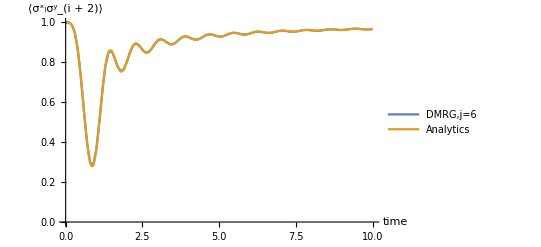

```mathematica
SetDirectory["~/3siteHam/Folded_XXZ_GS/"];
(*Data=Import["Data/Sav/DownUpUp/Correlation3.dat"];*)

Data=Import["Data/Sav/DownUpUp/Sz_profile.dat"];
Data=Drop[Data,1];
Data=DeleteCases[Data,_?(Length[#]<4&)];
column =2;

site=6;
shift=0;
flippedspin=3;
sign=Sign[r-flippedspin];
Data=Cases[Data,_?(#[[1]]==0+site&)];Data=Data[[;;,{8,column}]];
ZZ[t_,r_]:=1-2 (If[r-d<m,BesselJ[l-r+d,4 t]^2,0]+If[r+1>=m+d,BesselJ[l-r+d-1,4 t]^2,0]+If[m>r,BesselJ[l-r,4 t]^2,0]+If[m<=r+1,BesselJ[l-r-1,4 t]^2,0])/. {m->4,l->1,d->1};
XY[t_,r_]:=If[r<m,2 Cos[(1-d) Pi/2] BesselJ[l-r,4 t] BesselJ[l-r+d,4 t],0]+If[r>=m+d-1,2 Cos[(1-d) Pi/2] BesselJ[l-r-1,4 t] BesselJ[l-r+d-1,4 t],0]/. {m->4,l->1,d->1};
Z[t_,r_]:=1-2 HeavisideTheta[m-r-1/2] BesselJ[l-r,4 t]^2-2 HeavisideTheta[r+1-m+1/2] BesselJ[l-r-1,4 t]^2/.{m->4, l->1};




ListLinePlot[{Table[{Data[[k,1]],2Data[[k,2]]},{k,1,Length[Data]}]
(*,Table[{t,2BesselJ[-r-1Sign[r-flippedspin],4t]BesselJ[-r,4t]},{t,0,10,0.01}]*)
,Table[{t,Z[t,site/2]},{t,0,10,0.01}]
(*Sav*)

},PlotRange -> All,PlotLegends->{"DMRG,j="<>ToString[0+site],"Analytics"},AxesLabel -> {"time","⟨(σ^x)_i(σ^y)_(i + 2)⟩"}]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Sx0.dat",b]
```

~/Programs/Folded_XXZ_GS/code/Sx0.dat

```mathematica
a[[2,1]]
```

0.1

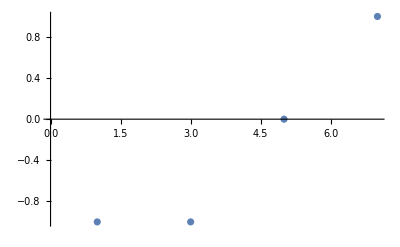

```mathematica
Dots={{0,0},{2,0},{5,0},{7,1}};
ListPlot[Dots]
```

```mathematica
1/(4/(π 6.))
```

4.71239

```mathematica
-0.95-458.6-40.00-80.00-0.09-45.59
```

-625.23

## Saverio Ising

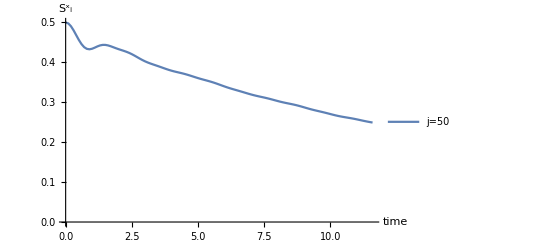

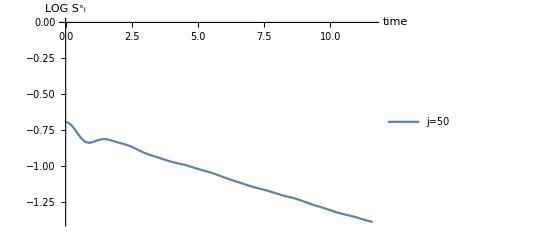

```mathematica
A=Import["~/Programs/Folded_XXZ_GS/Data/Ising/h0.5/SxSySz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
column =2;
site=50;
𝔸=Cases[A,_?(#[[1]]==0+site&)];a=𝔸[[;;,{6,column}]];

ListLinePlot[{
Table[{a[[i,1]],a[[i,2]]},{i,1,Length[a]}]

},PlotRange -> All,PlotLegends->{"j="<>ToString[0+site]},AxesLabel -> {"time","(S^x)_i"}]

ListLinePlot[{
Table[{a[[i,1]],Log[a[[i,2]]]},{i,1,Length[a]}]

},PlotRange -> All,PlotLegends->{"j="<>ToString[0+site]},AxesLabel -> {"time","LOG (S^x)_i"}]
```

```mathematica
a[[2,2]]
```

0.497535

~/Programs/Folded_XXZ_GS/code/Sx0.dat

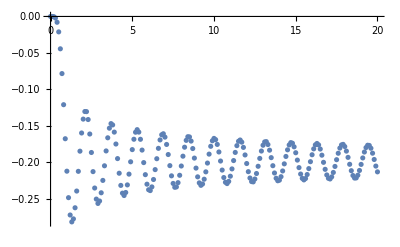

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Sx0.dat",b]
```

## NDsolve coupled rods

```mathematica
n = 499;

TMax=Floor[0.7n];

Subscript[x, 0][t_] := 0;
Subscript[x, n][t_] := 0;
eqns = Table[{
 (*Equation*)
(*Subscript[x, i]''[t] == -1/3Cos[Subscript[x, i][t]]( Sin[Subscript[x, i+1][t]] - 2 Sin[Subscript[x, i][t]] + Sin[Subscript[x, i-1][t]]), *)
Subscript[x, i]''[t] == -1/3( Subscript[x, i+1][t] + 2 Subscript[x, i][t] + Subscript[x, i-1][t]), 
(*Boundary conditions for velocities*)
 Subscript[x, i]'[0] == 0,
(*Boundary conditions for coordinates*)
If[i==Floor[n/2],Subscript[x, i][0] == 0.01,Subscript[x, i][0] == 0]
}, {i,n - 1}];
vars = Table[Subscript[x, i][t], {i, n-1}];
Solutions = NDSolve[eqns, vars, {t, 0, TMax}];

ListPlot3D[Table[vars /. First[Solutions], {t, 0, TMax,1}],PlotRange->All]
```

-Graphics3D-

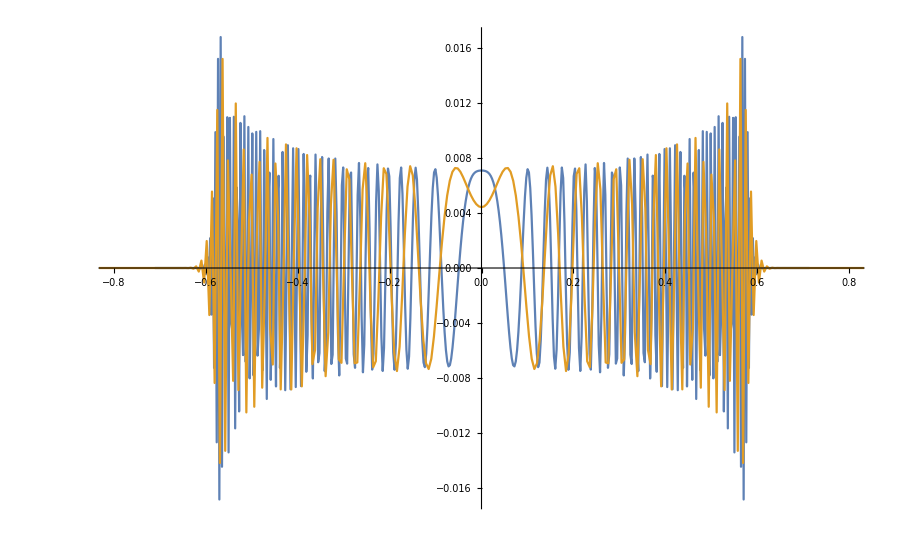

```mathematica
TimeSlice1=TMax; 
TimeSlice2=Floor[TMax/2];
DataTime1=vars /. First[Solutions]/. t->TimeSlice1; (*Substituting time into the NDSolve data*)
DataTime2=vars /. First[Solutions]/. t->TimeSlice2;
f[x_]:=Sqrt[x];

(*Forming an output as a table of pairs {coordinate, value}*)
Data1= Table[{(n-Length[DataTime1]/2)/TimeSlice1,f[TimeSlice1]*DataTime1[[n]]},{n,1,Length[DataTime1]}];
Data2= Table[{(n-Length[DataTime2]/2)/TimeSlice2,f[TimeSlice2]*DataTime2[[n]]},{n,1,Length[DataTime2]}];

ListPlot[{Data1,Data2},PlotRange->{{-0.8,0.8},Automatic},Joined-> True]
```

```mathematica
DataTime1[[1]]
```

1.90899×10^-15

## XXZ, Δ=0.4 ,<Z_i Z_(i+1)>

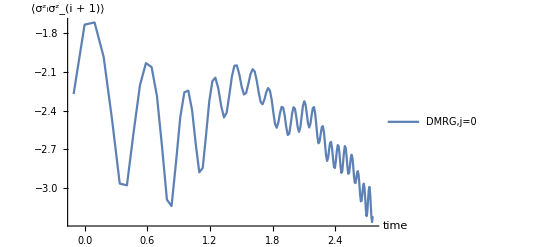

```mathematica
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
(*Data=Import["Data/Sav/DownUpUp/Correlation3.dat"];*)

Data=Import["XXZ/UUUDDD/Delta0.4_N300/Sz_profile.dat"];
Data=Drop[Data,1];
Data=DeleteCases[Data,_?(Length[#]<4&)];
column =3;

site=0;
shift=0;
Data=Cases[Data,_?(#[[1]]==0+site&)];Data=Data[[;;,{8,column}]];



ListLinePlot[{Table[{Log[Data[[k,1]]],Log[-4Data[[k,2]]]},{k,10,Length[Data]}]

},PlotRange -> All,PlotLegends->{"DMRG,j="<>ToString[0+site]},AxesLabel -> {"time","⟨(σ^z)_i(σ^z)_(i + 1)⟩"}]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/code/Sx0.dat",b]
```

~/Programs/Folded_XXZ_GS/code/Sx0.dat

```mathematica
a[[2,1]]
```

0.1

## XXZ ⟨Z_i Z_(i+1)⟩ for a single site

```mathematica
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
(*Data=Import["Data/Sav/DownUpUp/Correlation3.dat"];*)

site=0;
column =3;
(*
Data4=Import["XXZ/Global/Delta4_N150/Sz_profile.dat"];
Data4=Drop[Data4,1];
Data4=DeleteCases[Data4,_?(Length[#]<4&)];
Data4=Cases[Data4,_?(#[[1]]==0+site&)];
Data4=Data4[[;;,{8,column}]];

Data8=Import["XXZ/Global/Delta8_N150/Sz_profile.dat"];
Data8=Drop[Data8,1];
Data8=DeleteCases[Data8,_?(Length[#]<4&)];
Data8=Cases[Data8,_?(#[[1]]==0+site&)];
Data8=Data8[[;;,{8,column}]];

Data10=Import["XXZ/Global/Delta10_N150/Sz_profile.dat"];
Data10=Drop[Data10,1];
Data10=DeleteCases[Data10,_?(Length[#]<4&)];
Data10=Cases[Data10,_?(#[[1]]==0+site&)];
Data10=Data10[[;;,{8,column}]];

Data12=Import["XXZ/Global/Delta12_N150/Sz_profile.dat"];
Data12=Drop[Data12,1];
Data12=DeleteCases[Data12,_?(Length[#]<4&)];
Data12=Cases[Data12,_?(#[[1]]==0+site&)];
Data12=Data12[[;;,{8,column}]];
*)

(*
Data16=Import["XXZ/Global/Delta16_N150/Sz_profile.dat"];
Data16=Drop[Data16,1];
Data16=DeleteCases[Data16,_?(Length[#]<4&)];
Data16=Cases[Data16,_?(#[[1]]==0+site&)];
Data16=Data16[[;;,{8,column}]];
*)

Data6=Import["XXZ/Global/Delta6_N150/Sz_profile.dat"];
Data6=Drop[Data6,1];
Data6=DeleteCases[Data6,_?(Length[#]<4&)];
Data6=Cases[Data6,_?(#[[1]]==0+site&)];
Data6=Data6[[;;,{8,column}]];

Data14=Import["XXZ/Global/Delta14_N150/Sz_profile.dat"];
Data14=Drop[Data14,1];
Data14=DeleteCases[Data14,_?(Length[#]<4&)];
Data14=Cases[Data14,_?(#[[1]]==0+site&)];
Data14=Data14[[;;,{8,column}]];
```

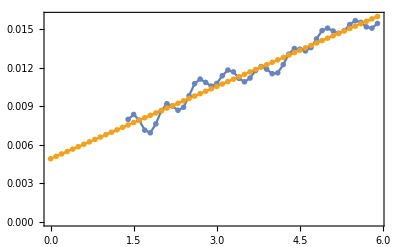

```mathematica
Needs["MaTeX`"]
<<MaTeX`

radius=0.015;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];

SciPostDarkBlue = Graphics[{RGBColor[36/255,75/255,105/255],Disk[]}];
SciPostBlack = Graphics[{RGBColor[0/255,0/255,0/255],Disk[]}];
SciPostRed = Graphics[{RGBColor[1,0.11,0.14],Disk[]}];


ListPlot[{
(*Table[{Data16[[k,1]],1-1},{k,1,Length[Data16]}]*)

(*,Table[{Data16[[k,1]],4Data16[[k,2]]},{k,1,Length[Data16]}]*)

(*,Table[{Data162[[k,1]],4Data162[[k,2]]},{k,1,Length[Data162]}]*)

(*Table[{Data12[[k,1]],0.006+0.0026Data12[[k,1]]},{k,1,Length[Data12]}],*)

(*Table[{Data4[[k,1]],(-4^2.5(4Data4[[k,2]]-1))},{k,1,Length[Data4]}],
Table[{Data8[[k,1]],(-8^2.5(4Data8[[k,2]]-1))},{k,1,Length[Data8]}],*)
Table[{Data14[[k,1]],((1-4Data14[[k,2]]))},{k,15,Length[Data14]}]
(*Table[{Data12[[k,1]],(-12^2(4Data12[[k,2]]-1))},{k,1,Length[Data12]}]*)
(*Table[{Data16[[k,1]],(-16^2.5(4Data16[[k,2]]-1))},{k,1,Length[Data16]}]
*)


,Table[{Data14[[k,1]],0.00491+0.001875Data14[[k,1]]},{k,1,Length[Data14]}]
}
,PlotRange->{{Automatic,Automatic},{Automatic,Automatic}}
,PlotStyle->PointSize[Medium]
,Joined->True
,Frame->True
,FrameStyle->BlackFrame
,Axes->{False,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","
\\langle \\sigma^z_{\\ell}\\sigma^z_{\\ell+1} \\rangle_{\\rm Folded}
-
\\langle \\sigma^z_{\\ell}\\sigma^z_{\\ell+1} \\rangle_{\\rm XXZ}
"},FontSize->35]
,LabelStyle->Directive[FontSize->25]
,PlotLegends->{Placed[MaTeX[{
"Test",
"\\Delta = 12",
"\\Delta = 8",
"\\Delta = 4"

},FontSize->20],{0.7,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow,radius},
{SciPostRed,radius}
(*,{RED0, radius}*)
}

]
```

{a→0.243124,b→1.31136}

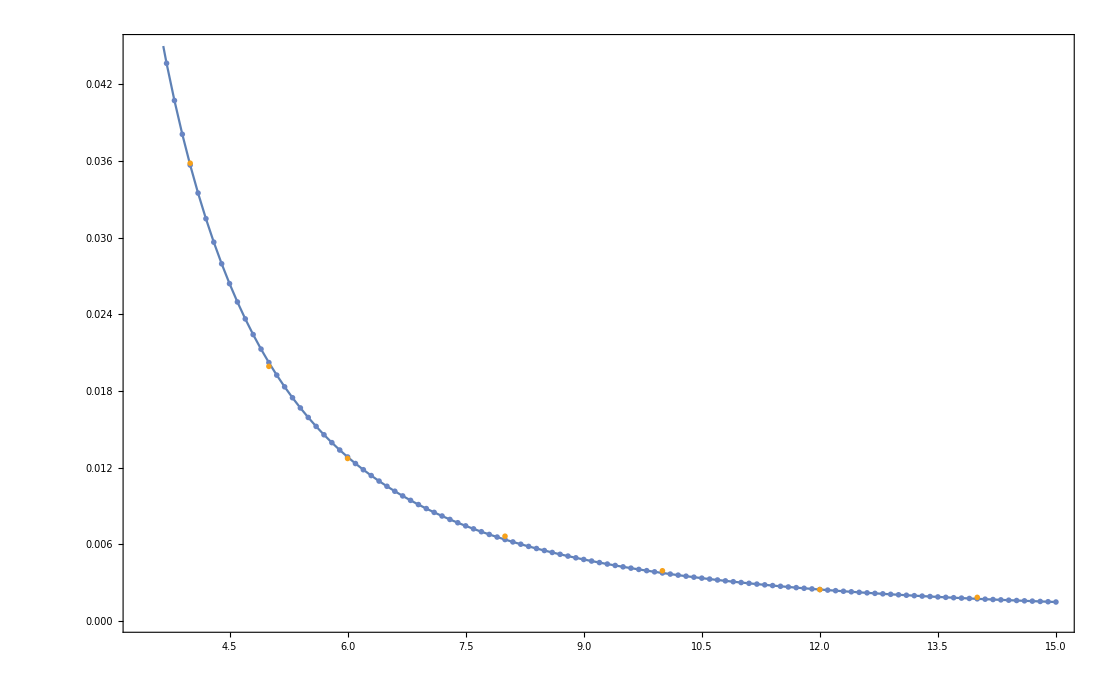

```mathematica
Slopes={{4,(*0.035*)0.035826066502629976},{5,(*0.022*)0.01991877493563023},{6,(*0.0128*)0.012706368796867599},{8,(*0.007*)0.006621196456420364},{10,0.003916420627686344},{12,0.00244012228924986},{14,0.0018336109115256118}};

FIT = FindFit[Slopes,a x^-2+b x^(-2-1) ,{a,b},x]
ListPlot[{
Table[{n,(a/.FIT)n^-2+(b/.FIT)n^(-2-1)},{n,3,Slopes⟦-1,1 ⟧+1,0.1}],
(*Table[{n,Exp[-0.9] n^-2},{n,3,Slopes⟦-1,1 ⟧+1,0.1}],*)
Slopes
}
,PlotRange->{{3.38,Automatic},{0,0.045}}
,PlotStyle->PointSize[Medium]
,Joined->{True,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{False,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\Delta","\\alpha"},FontSize->35]
,LabelStyle->Directive[FontSize->25]
,PlotLegends->{Placed[MaTeX[{
"\\rm Fit",
"\\rm Numerics"
},FontSize->20],{0.7,0.6}]}
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow,3radius}
}

]
```

```mathematica
Length[Data5]
```

101

{k→0.00183361,b→0.00510469}

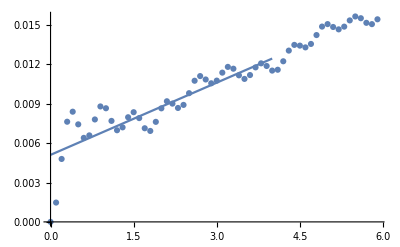

{a→0.000546695,b→-0.0000408803}

```mathematica
Data5=Import["XXZ/Global/Delta14_N150/Sz_profile.dat"];
Data5=Drop[Data5,1];
Data5=DeleteCases[Data5,_?(Length[#]<4&)];
Data5=Cases[Data5,_?(#[[1]]==0+site&)];
Data5=Data5[[;;,{8,column}]];
Linear=FindFit[Table[{Data5[[k,1]],((1-4Data5[[k,2]]))},{k,20,60}],k x+b ,{k,b},x]
Show[ListPlot[Table[{Data5[[k,1]],((1-4Data5[[k,2]]))},{k,1,Length[Data5]}]],
Plot[(k/.Linear) *x + b/.Linear,{x,0, 4}]
]
```

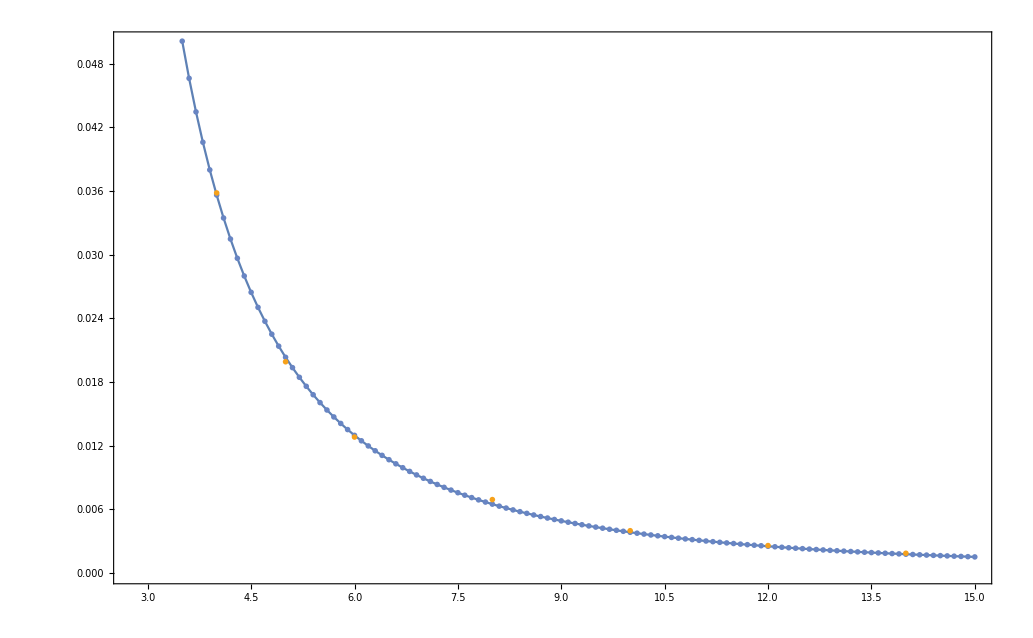

```mathematica
ListPlot[{
Table[{n,(a/.FIT)n^-2+(b/.FIT)n^(-2-1)},{n,3,Slopes⟦-1,1 ⟧+1,0.1}],
(*Table[{n,Exp[-0.9] n^-2},{n,3,Slopes⟦-1,1 ⟧+1,0.1}],*)
Slopes
}
,PlotRange->{Automatic,{0,0.05}}
,PlotStyle->PointSize[Medium]
,Joined->{True,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{False,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\Delta","\\alpha"},FontSize->35]
,LabelStyle->Directive[FontSize->25]
,PlotLegends->{Placed[MaTeX[{
"\\rm Fit",
"\\rm Numerics"

},FontSize->20],{0.7,0.6}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow,3radius}
(*{SciPostRed,radius}*)
(*,{RED0, radius}*)
}

]
```

```mathematica
Export["~/Programs/Folded_XXZ_GS/Pictures/Simply_Jammed/Picture.pdf",%]
```

~/Programs/Folded_XXZ_GS/Pictures/Simply_Jammed/Picture.pdf

{k→0.0128241,b→0.0260326}

{a→0.000546695,b→-0.0000408803}

```mathematica
Log[Slopes]
```

{{Log[4],-3.35241},{Log[5],-3.81671},{Log[8],-4.96185},{Log[10],-5.52146},{Log[12],-5.95224}}

## NEEL state with spin flip

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/Neel/"];
Neel0=Import["Neel_1_0/Sz_profile.dat"];
Neel0=Drop[Neel0,1];
Neel0=DeleteCases[Neel0,_?(Length[#]<4&)];
Neel0=Chop[Neel0[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

Neel01=Import["Neel_1_1/Sz_profile.dat"];
Neel01=Drop[Neel01,1];
Neel01=DeleteCases[Neel01,_?(Length[#]<4&)];
Neel01=Chop[Neel01[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)

Neel010=Import["Neel_1_19/Sz_profile.dat"];
Neel010=Drop[Neel010,1];
Neel010=DeleteCases[Neel010,_?(Length[#]<4&)];
Neel010=Chop[Neel010[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

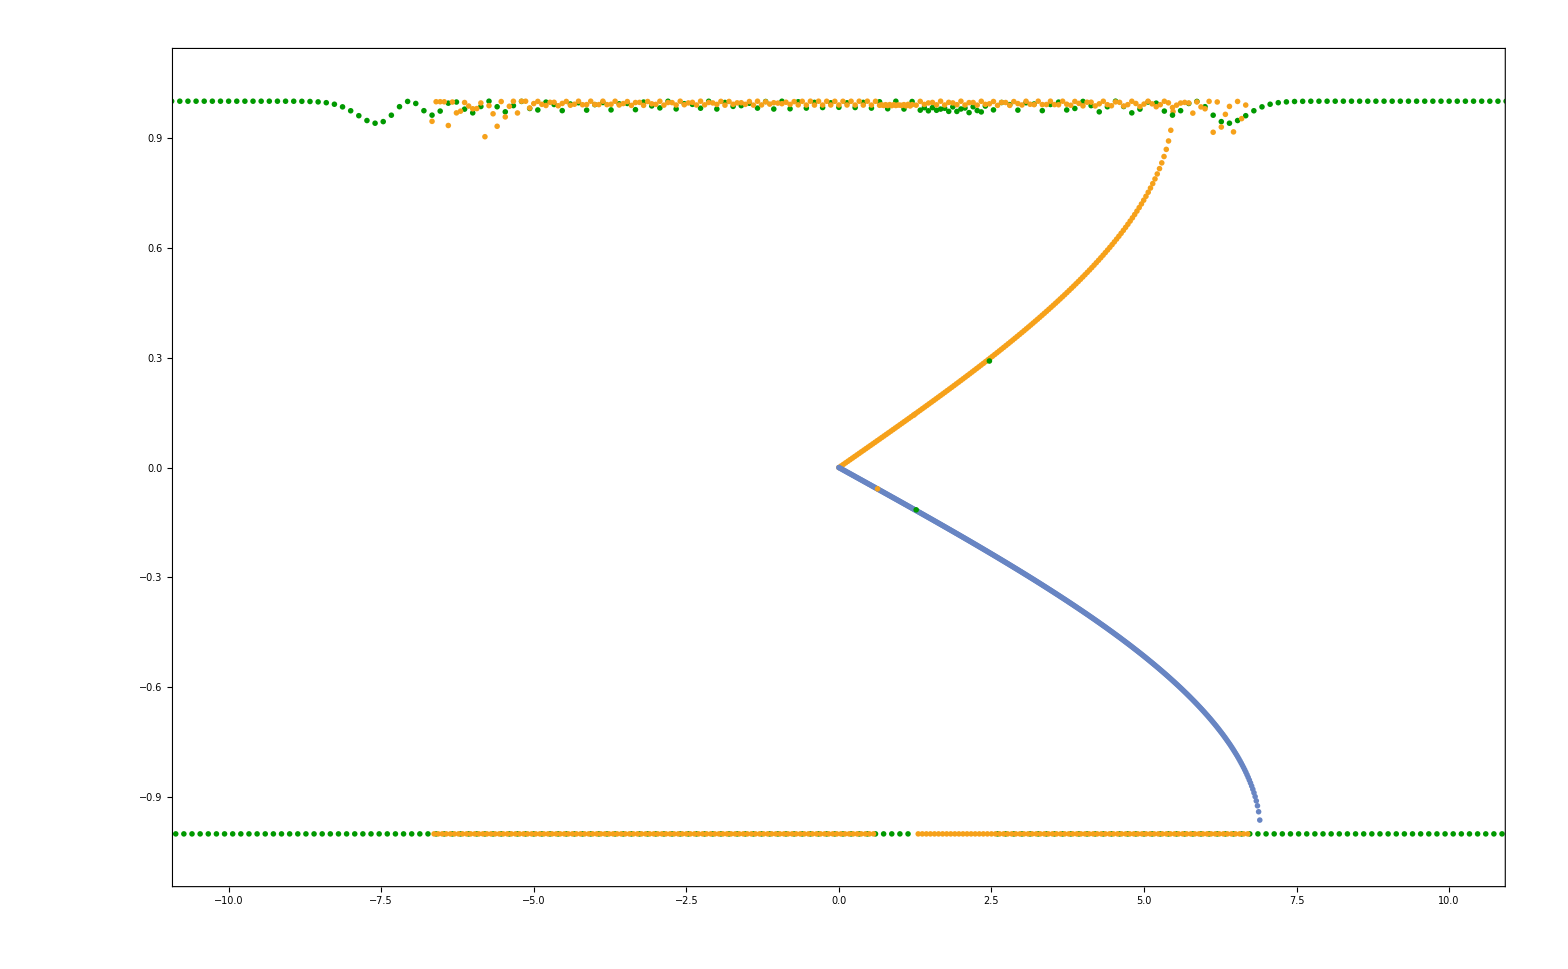

```mathematica
Needs["MaTeX`"]
<<MaTeX`

Sites=Neel010[[;;,1]];
Sites=Union[Sites];
SystemSizeNeel =Length[Sites]; 
xminNeel=1;
xmaxNeel=SystemSizeNeel;

timestep=0.1;
Time =15.;
TimeSlice = Time/timestep;
TimeSlice2 = 2Time/timestep;
SHIFT=1;(*technical part:  point types etc *)
radius=0.01;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];


RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],widht}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostGreen = Graphics[{RGBColor[0/255,153/255,0/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];

everypoint=1;



DataNeel0[l_,time_,col_]:=Neel0[[l+SystemSizeNeel*Floor[time],col]];
ObsNeel0[l_,time_]:= 2 DataNeel0[l,time,2];

DataNeel01[l_,time_,col_]:=Neel01[[l+SystemSizeNeel*Floor[time],col]];
ObsNeel01[l_,time_]:= 2 DataNeel01[l,time,2];

DataNeel010[l_,time_,col_]:=Neel010[[l+SystemSizeNeel*Floor[time],col]];
ObsNeel010[l_,time_]:= 2 DataNeel010[l,time,2];
la=19;(*19*)
lb=37;(*37*)
mprime=11;
M=9;
xodd[l_]:=Piecewise[{{l, l≤mprime},{mprime+2(l-mprime),l>mprime&& l≤ mprime+M},{l+M,l>mprime+M}}];

xodd1[l_]:=l ;
xodd2[l_]:=mprime+2(l-mprime);
xlen[l_]:=Piecewise[{{l/2,l≤la-1},{l-(la-1)/2,l>la&&l≤lb},{(l+(lb-la+1))/2,l>lb}}];
FIG=ListPlot[{
(*Join[Table[{ζ,2/π ArcSin[25.0/(4*10)](*2/π ArcSin[ζ/v]*)},{ζ,-10,10,0.01}],Table[{ζ,-2/πArcSin[ζ/v]},{ζ,-10,10,0.01}]],*)


(*Join[Table[{ζ,2/π ArcSin[ζ/v]},{ζ,-10,10,0.01}],Table[{ζ,-2/πArcSin[ζ/v]},{ζ,-10,10,0.01}]],
*)
(*Join[Table[{l/Time,-2/πArcSin[l/(8 Time)]},{l,-300,la-1}],Table[{l/Time,2/π ArcSin[l/(8 Time)]},{l,-300,la-1}],
Table[{l/Time,2/π ArcSin[(l-(la-1)/2)/(4 Time)]},{l,la,lb}],Table[{l/Time,-2/πArcSin[(l-(la-1)/2)/(4 Time)]},{l,la,lb}],
Table[{l/Time,2/π ArcSin[(l+(lb-la+1))/(8 Time)]},{l,lb,300}],Table[{l/Time,-2/πArcSin[(l+(lb-la+1))/(2 *4 Time)]},{l,lb,300}]],*)


(*Join[Table[{18tinverse,-2/πArcSin[xodd[(18+1)/2]/4 tinverse]},{tinverse,0,100,0.001}],
(*Table[{18tinverse,2/π ArcSin[xodd[(18+1)/2]/4 tinverse]},{tinverse,-100,0,0.001}],*)
Table[{36tinverse,2/π ArcSin[xodd[(36+1)/2]/4 tinverse]},{tinverse,0,100,0.001}]
(*Table[{36tinverse,-2/πArcSin[xodd[(36+1)/2]/4 tinverse]},{tinverse,-100,0,0.001}]*)

],
*)
Table[{(2mprime+2M-3)tinverse,2/π ArcSin[mprime/4 tinverse (1+2(M-1)/mprime)]},{tinverse,0,100,0.001}],
Table[{(2mprime-3)tinverse,-2/π ArcSin[mprime/4 tinverse ]},{tinverse,0,100,0.001}],

(*Join[Table[{l/(TimeSlice timestep),2/π ArcSin[xodd[(l+1)/2]/(4 (TimeSlice timestep))]},{l,-810,810}],Table[{l/(timestep TimeSlice),-2/πArcSin[xodd[(l+1)/2]/(4 (TimeSlice timestep))]},{l,-800,800}]],*)



Table[{(DataNeel010[l,TimeSlice,1]+SHIFT)/(TimeSlice*timestep), (ObsNeel010[l,TimeSlice])},{l,xminNeel,xmaxNeel,everypoint}],
Table[{(DataNeel010[l,2TimeSlice,1]+SHIFT)/(2TimeSlice*timestep), (ObsNeel010[l,2TimeSlice])},{l,xminNeel,xmaxNeel,everypoint}]

(*

Join[Table[{l/(TimeSlice2 timestep),2/π ArcSin[xodd[(l+1)/2]/(4 (TimeSlice2 timestep))]},{l,0,810}],Table[{l/(timestep TimeSlice2),-2/πArcSin[xodd[(l+1)/2]/(4 (TimeSlice2 timestep))]},{l,0,100}]],



Table[{(DataNeel010[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep), (ObsNeel010[l,TimeSlice2])},{l,xminNeel,xmaxNeel,everypoint}],

Table[{l/(timestep TimeSlice),-2/πArcSin[xodd[(l+1)/2]/(4 (TimeSlice timestep))]},{l,0,100}]*)






(*Table[{(DataNeel010[l,TimeSlice,1]+SHIFT)/(TimeSlice*timestep), (ObsNeel010[l,TimeSlice])},{l,xminNeel,xmaxNeel,everypoint}]*)

},
PlotRange->{{-10.5,10.5},{-1.1,1.1}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{False,False,False},
Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\ell/t","\\langle \\sigma^z_{\\ell}\\rangle"},FontSize->35],
LabelStyle->Directive[FontSize->25],
PlotLegends->{Placed[MaTeX[{
"t="<>ToString[TimeSlice*timestep],
"t="<>ToString[2TimeSlice*timestep],
"{\\rm Trajectory}"
},FontSize->20],{0.5,0.15}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
(*{BLACK,radius}*)
{SciPostYellow,radius},
{SciPostBlue,radius},
{SciPostGreen,radius}
(*,{RED0, radius}*)
}

 ]
```

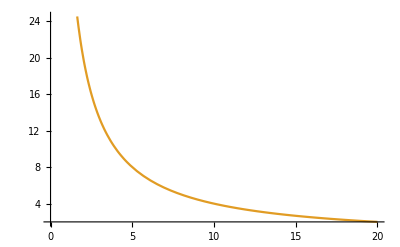

```mathematica
Plot[{ArcSin[xodd[(30+1)]/t],xodd[(30+1)]/t},{t,0,20}]
```

```mathematica
2mprime+2M
```

38

## XP model

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["XP/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

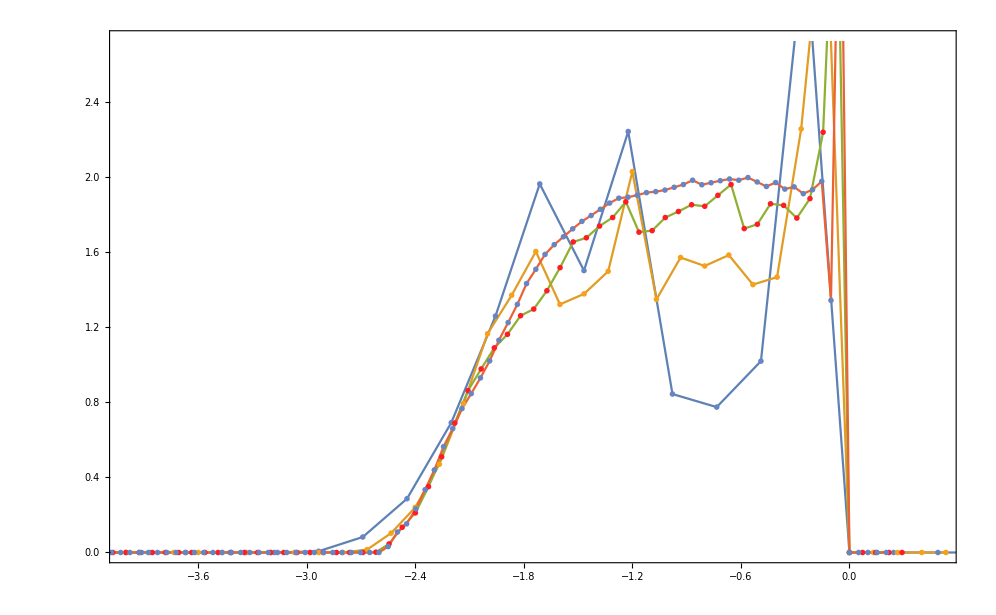

```mathematica
Needs["MaTeX`"]

Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

timestep=0.1;

Time = 5;

TimeSlice1 = Time/timestep;
TimeSlice2 = 2Time/timestep;
TimeSlice4 = 4Time/timestep;
TimeSlice6 = 6Time/timestep;
TimeSliceXXZ5 =Time/timestep;
TimeSliceXXZ10 = Time/(timestep (*π/(4 *10.)*));
SHIFT=-55;(*technical part:  point types etc *)

radius=0.01;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],widht}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];

everypoint=1;

exp=7./8;

DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= time^(1-exp)(2 DataFolded[l,time,2]+1.0);




FIG=ListPlot[{
Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep)^exp, (ObsFolded[l,TimeSlice1])},{l,xminFolded,xmaxFolded,everypoint}]
,Table[{(DataFolded[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep)^exp, (ObsFolded[l,TimeSlice2])},{l,xminFolded,xmaxFolded,everypoint}]
,Table[{(DataFolded[l,TimeSlice4,1]+SHIFT)/(TimeSlice4*timestep)^exp, (ObsFolded[l,TimeSlice4])},{l,xminFolded,xmaxFolded,everypoint}]
,Table[{(DataFolded[l,TimeSlice6,1]+SHIFT)/(TimeSlice6*timestep)^exp, (ObsFolded[l,TimeSlice6])},{l,xminFolded,xmaxFolded,everypoint}]

},
PlotRange->{{-4,0.5},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{True,True}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\zeta=\\ell/ t^{"<>ToString[exp]<>"}","t^"<>ToString[1-exp]<>"\\langle \\sigma^z_{\\ell} \\rangle"},FontSize->35],
LabelStyle->Directive[FontSize->25],
PlotLegends->{Placed[MaTeX[{
"\\frac{1}{2}X_i(1+Z_{i+1});(t="<>ToString[TimeSlice1*timestep]<>")"
,"\\frac{1}{2}X_i(1+Z_{i+1});(t="<>ToString[TimeSlice2*timestep]<>")"
,"\\frac{1}{2}X_i(1+Z_{i+1});(t="<>ToString[TimeSlice4*timestep]<>")"
,"\\frac{1}{2}X_i(1+Z_{i+1});(t="<>ToString[TimeSlice6*timestep]<>")"
},FontSize->20],{0.2,0.75}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{
{SciPostBlue,radius}
,{SciPostYellow,radius}
,{RED0, radius}
}

 ]
```

## XP for a single site

```mathematica
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
(*Data=Import["Data/Sav/DownUpUp/Correlation3.dat"];*)

site=0;
column =3;

Data=Import["XP/Sz_profile.dat"];
Data=Drop[Data,1];
Data=DeleteCases[Data,_?(Length[#]<4&)];
Data=Cases[Data,_?(#[[1]]==0+site&)];
Data=Data[[;;,{4,column}]];

(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["XP/Sz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

```mathematica
Needs["MaTeX`"]
<<MaTeX`

radius=0.015;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];
SciPostBlack = Graphics[{RGBColor[0/255,0/255,0/255],Disk[]}];
SciPostRed = Graphics[{RGBColor[1,0.11,0.14],Disk[]}];

ListPlot[{
Table[{Data[[k,1]],1.3/Data[[k,1]]},{k,2,Length[Data]}],
Table[{Data[[k,1]],-1.25/Data[[k,1]]},{k,2,Length[Data]}],
Table[{Data[[k,1]],4Data[[k,2]]},{k,1,Length[Data]}]
}
,PlotRange->{{0,50},{Automatic,Automatic}}
,PlotStyle->PointSize[Medium]
,Joined->{True,True,False}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{False,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"t","\\langle {\\mathcal{Q}}_{\\ell} \\rangle"},FontSize->35]
,LabelStyle->Directive[FontSize->25]
,PlotLegends->{Placed[MaTeX[{
"1/t",
"\\ell = 0"


},FontSize->20],{0.8,0.15}]}
(*,FrameTicks->{
{{0,0.1,0.2,0.3},None},
{{-6,-4,-2,0,2,4,6},None}}*)

,PlotMarkers->{

{SciPostBlue,radius},
{SciPostBlue,radius},
{SciPostYellow,radius}


}

]
```

-Graphics-

## PPK model

```mathematica
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["PPK/L4/N200_1/SxSySz_profile.dat"];
A=Drop[A,1];
𝔸=DeleteCases[A,_?(Length[#]<4&)];
A=Chop[𝔸[[;;,{1,2,3,4}]]]; (*l, Subscript[Z, i], Subscript[Z, i] Subscript[Z, i+1], Subscript[Z, i] Subscript[Z, i+2], Subscript[Z, i] Subscript[Z, i+3], Subscript[Z, i] Subscript[Z, i+4], (-1)^i Subscript[Z, i] *)
```

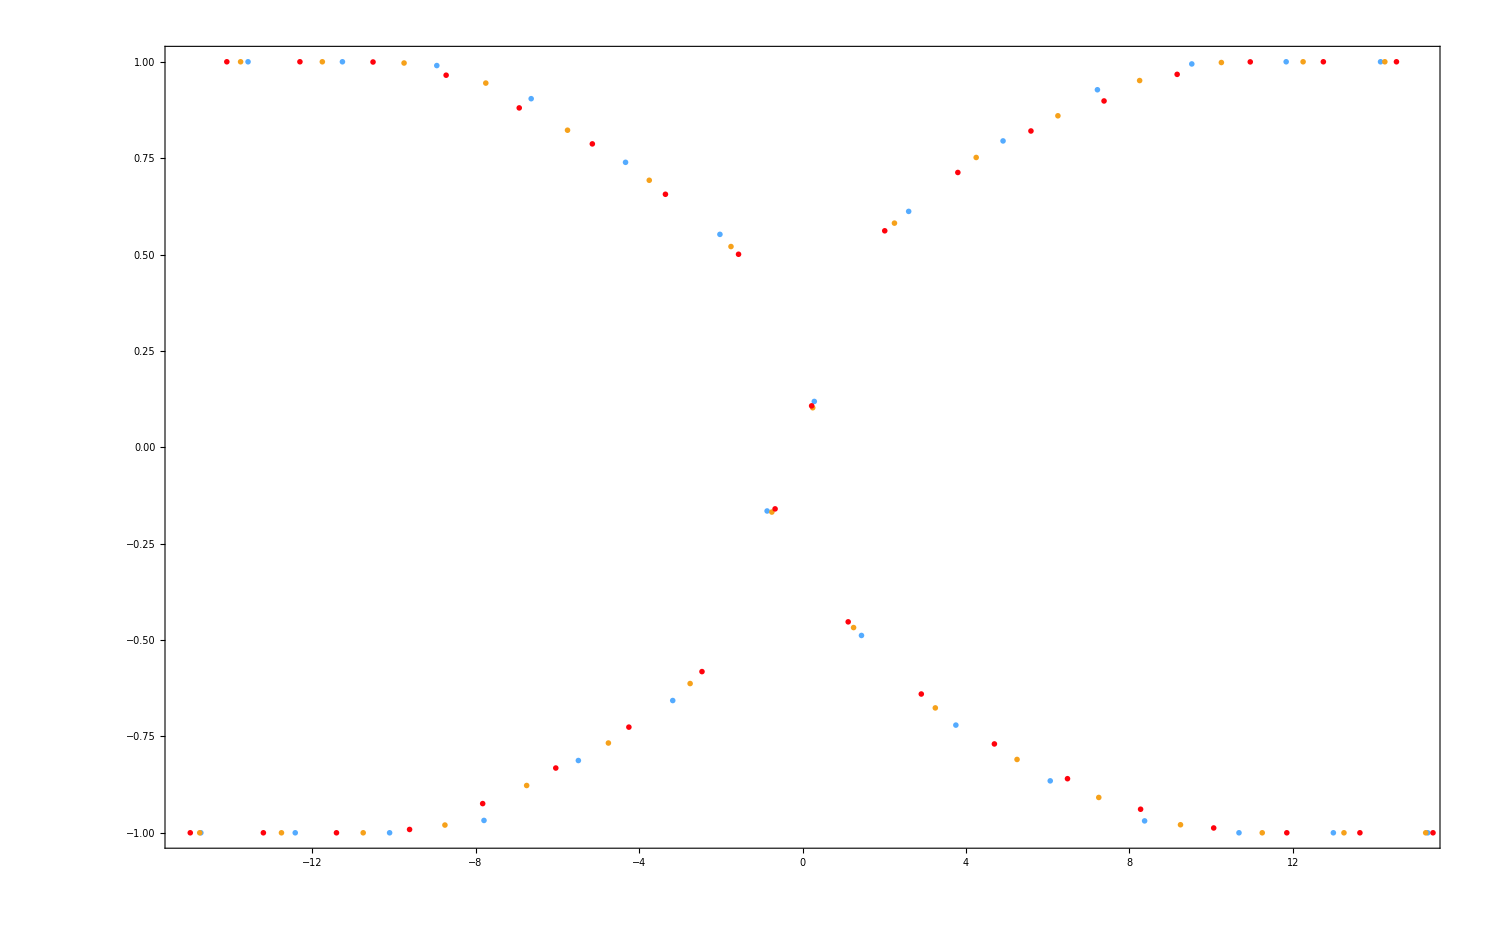

```mathematica
Needs["MaTeX`"]

Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSizeFolded =Length[Sites]; 
xminFolded=1;
xmaxFolded=SystemSizeFolded;

timestep=0.1;

Time = 1;
TimeSlice1 = 3Time/timestep;
TimeSlice2 = 4Time/timestep;
TimeSlice3 = 5Time/timestep;
SHIFT=0.5;(*technical part:  point types etc *)

radius=0.01;
widht=Thickness[0];
CircleEdgeWidht=Thickness[0.15];
<<MaTeX`

RED0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[255/255,2/255,12/255],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,Disk[]}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[84/255,171/255,1],widht,Disk[]}];
BLACK=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[0,0,0],widht}];
SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];

everypoint=2;

exp=0.5;
column = 2;
DataFolded[l_,time_,col_]:=A[[l+SystemSizeFolded*Floor[time],col]];
ObsFolded[l_,time_]:= (2 DataFolded[l,time,column]);
direction="";
If[column ==2,direction = "x"];
If[column ==3,direction = "y"];
If[column ==4,direction = "z"];

FIG=ListPlot[{
Table[{(DataFolded[l,TimeSlice1,1]+SHIFT)/(TimeSlice1*timestep)^exp, (ObsFolded[l,TimeSlice1])},{l,xminFolded+1,xmaxFolded,everypoint}]
,Table[{(DataFolded[l,TimeSlice2,1]+SHIFT)/(TimeSlice2*timestep)^exp, (ObsFolded[l,TimeSlice2])},{l,xminFolded+1,xmaxFolded,everypoint}]
,Table[{(DataFolded[l,TimeSlice3,1]+SHIFT)/(TimeSlice3*timestep)^exp, (ObsFolded[l,TimeSlice3])},{l,xminFolded+1,xmaxFolded,everypoint}]

},
PlotRange->{{-15,15},{Automatic,Automatic}},
(*AxesLabel -> {"x/t","Spin operator"},*)(*PlotLegends->{"Sx, t="<>ToString[TimeSlice/10],"Sy","Sz"},*)
PlotStyle->PointSize[Medium],

Joined->{False,False,False}
,Frame->True,
FrameStyle->BlackFrame,
Axes->{False,False},
BaseStyle->{FontFamily->"Latin Modern Roman"},
FrameLabel->MaTeX[{"\\zeta=\\ell/ t^{"<>ToString[exp]<>"}","\\langle \\sigma^{"<>direction<>"}_{\\ell} \\rangle"},FontSize->35],
LabelStyle->Directive[FontSize->25],
PlotLegends->{Placed[MaTeX[{
"folded + PPK;(t="<>ToString[TimeSlice1*timestep]<>")"
,"folded + PPK;(t="<>ToString[TimeSlice2*timestep]<>")"
,"folded + PPK;(t="<>ToString[TimeSlice3*timestep]<>")"
},FontSize->20],{0.15,0.65}]},
PlotMarkers->{
{BLUE0,radius}
,{SciPostYellow,radius}
,{RED0, radius}
}
,ImageSize->1500
 ]
```

```mathematica
4*Exp[1.12*4]
```

352.939

```mathematica
Exp[0.846*6+1.3]
```

587.573

## PPK Jamming criterium ⟨(1-(σ^z)_l)/2(1-(σ^z)_(l+1))/2⟩≡[⟨(σ^z)_l(σ^z)_(l+1)⟩ – ⟨(σ^z)_l⟩-⟨(σ^z)_(l+1)⟩ ++1 ]/4 Profile

```mathematica
Needs["MaTeX`"];
<<MaTeX`
(*SetDirectory["/home/kbidzhiev/3siteHam/Folded_XXZ_GS/Data/"];*)
SetDirectory["~/Programs/Folded_XXZ_GS/Data/"];
A=Import["PPK/L4/N200_1/Sz_profile.dat"];
A=Drop[A,1];
A=DeleteCases[A,_?(Length[#]<4&)];
A=A[[;;,{1,2,3}]]; (*l, Subscript[σ^z, l], Subscript[σ^z, l] Subscript[σ^z, l+1]*)
Sites=A[[;;,1]];
Sites=Union[Sites];
SystemSize =Length[Sites]; 
xmin=1;
xmax=SystemSize-1;(* cause Subscript[σ^z, l+1] can ∃ l < SystemSize-1 *)
```

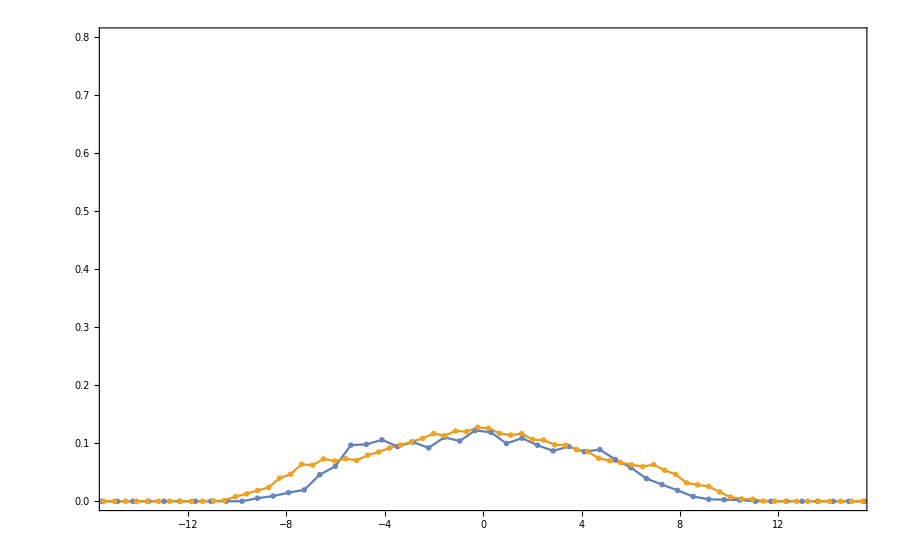

```mathematica
SHIFT=1.5; (*To match 0 in data with 0 on the plot*)
timestep=0.1(*0.011193*);
TimeSlice0=10;
TimeSlice1=2.5/timestep;
TimeSlice2=5/timestep;


radius=0.01;
widht=Thickness[0.002];
CircleEdgeWidht=Thickness[0.009];
CROSSd ={AbsoluteThickness[radius/8],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]};
CROSS ={AbsoluteThickness[radius/8],Line[{{0,-1},{0,1}}],Line[{{-1,0},{1,0}}]};
DIAMOND = Polygon[{{1,0},{0,1},{-1,0},{0,-1}}];

RED0=Graphics[{EdgeForm[CircleEdgeWidht],RGBColor[1,0.11,0.14],widht,Disk[]}];
GREEN0=Graphics[{RGBColor[4/255,180/255,49/255],widht,DIAMOND}];
BLUE0=Graphics[{(*EdgeForm[CircleEdgeWidht],*)RGBColor[51/255,153/255,1],widht,Disk[]}];
BLACK=Graphics[{RGBColor[0,0,0],Disk[]}];


SciPostYellow = Graphics[{RGBColor[246/255,161/255,26/255],Disk[]}];
SciPostBlue = Graphics[{RGBColor[104/255,133/255,195/255],Disk[]}];

exp = 0.5;

Sigma[n_,col_,time_]:=A[[n+SystemSize*Floor[time],col]];
Obs[n_,time_]:=(timestep time)^(1-exp)( 4Sigma[n,3,time]  -2(Sigma[n+1,2,time] +Sigma[n,2,time])  + 1)/4;
FIG=ListPlot[{


(*Table[{n,0.16/(√(1-(n/6)^2))},{n,-5.9,5.9,0.1}]
(*,Table[{n,0.32/(√(12/π Sin[π (n+6)/12]))},{n,-15.9,15.9,0.01}]*)
*)
Table[{(A[[n+SystemSize*Floor[TimeSlice1],1]]+SHIFT)/(TimeSlice1*timestep)^exp,Obs[n,TimeSlice1]},{n,xmin+1,xmax,1}],
Table[{(A[[n+SystemSize*Floor[TimeSlice2],1]]+SHIFT)/(TimeSlice2*timestep)^exp,Obs[n,TimeSlice2]},{n,xmin+1,xmax,1}]


},
Joined->{True,True}
,Frame->True
,FrameStyle->BlackFrame
,Axes->{True,False}
,BaseStyle->{FontFamily->"Latin Modern Roman"}
,FrameLabel->MaTeX[{"\\zeta=\\ell/ t^{"<>ToString[exp]<>"}","t^{"<>ToString[1-exp]<>"}\\mathcal{P}_{\\downarrow \\downarrow}(\\ell/t)"},FontSize->35]

,LabelStyle->Directive[FontSize->25]
,LABELS={
"folded + \\sqrt(2)PPK; t="<>ToString[TimeSlice1*timestep]
,"folded + \\sqrt(2)PPK; t="<>ToString[TimeSlice2*timestep]
};
PlotLegends->Placed[MaTeX[LABELS,FontSize -> 30],{0.5,0.8}]
,PlotRange->{{-15,15},{Automatic,0.8(*0.025*)}}
(*,FrameTicks->{
{{0,{0.02,""},{0.04,""},{0.06,""},{0.08,""}
,0.1,{0.12,""},{0.14,""},{0.16,""},{0.18,""}
,0.2,{0.22,""},{0.24,""},{0.26,""},{0.28,""}
,0.3},None},
{(*{-6,-4,-2,0,2,4,6}*)Automatic,None}}*)
(*PlotStyle->{RGBColor[1,0.11,0.14],RGBColor[4/255,180/255,49/255],RGBColor[51/255,153/255,1]},*)
,PlotMarkers->{
{SciPostBlue,radius},
{SciPostYellow, radius},
{RED0,0.01}
}

 ]
```